```mathematica
string=NotebookDirectory[];
FileTensorAnalysis=string<>"TensorAnalysis.nb";
FileFuncao1=string<>"Funcao1.nb";
FileFuncao2=string<>"Funcao2.nb";
vecStrings={FileTensorAnalysis,FileFuncao1,FileFuncao2};
For[is=1,is≤Length[vecStrings],is++,
nb=NotebookOpen[vecStrings[[is]]];
SelectionMove[nb,All,Notebook];
SelectionEvaluate[nb];
NotebookClose[nb];
]
```

```mathematica
Function1[Log[A/C]/B/.exemple,0]
LFunction[EpsEqL[Log[A/C]/B/.exemple]]
```

-2.77556×10^-17

0.490305

```mathematica
ElastoPlasticL[L_,EP_,ETotal_]:=Block[{Lnext,θnext,EPnext,valf1,valf2,SigI1xJ2,SigTrial,EElast,EElastIJ,delL,I1next,J2next,lval,diffsig,diffsigIJ,sigresult,IJQuadrant,epsp,epsprev,epsmax,pr},
pr=True;
Lnext=L;
EElast=ETotal-EP;
EElastIJ=ToIJ[EElast];
IJQuadrant=EElastIJ[[3]];
SigI1xJ2={3 K EElastIJ[[1]],2G EElastIJ[[2]],IJQuadrant}/.exemple;
SigTrial=FromIJ[SigI1xJ2];
valf1=Function1[SigI1xJ2[[1]],SigI1xJ2[[2]]] // Chop;
valf2=Function2L[SigI1xJ2[[1]],SigI1xJ2[[2]],L]//Chop;
epsmax=2;
If[pr,
Print["ETotal = ",ETotal];
Print["SigI1xJ2 = ",SigI1xJ2];
Print["L ",L];
Print["valf1 = ",valf1];
Print["valf2 = ",valf2];
];
If[(valf2≤ 0 && SigI1xJ2[[1]] ≤  L) || (valf1 ≤ 0 && SigI1xJ2[[1]] ≥ L),
Print["Elastic"];
Lnext = L;
sigresult=FromIJ[SigI1xJ2];
EPnext=EP
,If[valf2 >0 && SigI1xJ2[[1]] ≤ L,
Print["Project F2"];
{θnext,delL}=NewtonFuncL[L,SigI1xJ2];
Lnext=L+delL;
lval=Lnext;
I1next=lval+F[lval]R Cos[θnext]/.exemple;
J2next=F[lval]Sin[θnext]/.exemple;
Print["Function2L = ",Function2L[I1next,J2next,Lnext]];
sigresult=FromIJ[{I1next,J2next,IJQuadrant}];
diffsig=FromIJ[SigI1xJ2]-FromIJ[{I1next,J2next,IJQuadrant}];
diffsigIJ=ToIJ[diffsig];
EPnext=EP+FromIJ[{diffsigIJ[[1]]/(3 K),diffsigIJ[[2]]/(2G),diffsigIJ[[3]]}]/.exemple;
,
Print["Project F1"];
I1next=NewtonF1[SigI1xJ2];
J2next = F[I1next]/.exemple;
If[J2next<0,
Print["Point is wasted J2next = ",J2next];
I1next=Log[A/C]/B/.exemple;
J2next = 0.;
epsmax=EpsEqL[I1next]/.exemple;
Print[" eps max ",epsmax];
];
Print["Function 1 I1next ",I1next," J2next ",J2next," value ",Function1[I1next,J2next]];
sigresult=FromIJ[{I1next,J2next,IJQuadrant}];
diffsig=FromIJ[SigI1xJ2]-sigresult;
diffsigIJ=ToIJ[diffsig];
EPnext=EP+FromIJ[{diffsigIJ[[1]]/(3K),diffsigIJ[[2]]/(2G),diffsigIJ[[3]]}]/.exemple;
epsprev = EpsEqL[L]/.exemple;
epsp=epsprev+diffsigIJ[[1]]/(3K)/.exemple;
If[epsp > epsmax,epsp=epsmax];
Lnext=LFunction[epsp]/.exemple;
Print["epsprev ",epsprev, " epspnext ",epsp," Lprev ",L," Lnext ",Lnext]; 
If[I1next<Lnext,Print["******* Should have projected onto F2 ***********"]];.08 
]
];
{Lnext,EPnext,sigresult,SigTrial}
]
locL=LFunction[0]
EP={0,0};

ETotal={0.05/3,0.0};
ElastoPlasticL[0,EP,ETotal]

ETotal={-0.065/50,0.0};
ElastoPlasticL[locL,EP,ETotal]
```

0.133045

ETotal = {0.0166667,0.}

SigI1xJ2 = {3.33333,0.7698,-1}

L 0

valf1 = 2.19937

valf2 = 482.749

Project F1

sigtrial {3.33333,0.7698,-1}

I1 start value 0.8

I1Val = 0.792513

F[I1] = -0.0561087

Diffval = 0.

Point is wasted J2next = -0.0561087

eps max 0.0256667

Function 1 I1next 0.490305 J2next 0. value -2.77556×10^-17

epsprev -0.00730205 epspnext 0.00691309 Lprev 0 Lnext 0.24382

{0.24382,{0.0158495,-0.000817174},{0.163435,0.163435},{2.,0.666667}}

ETotal = {-0.0013,0.}

SigI1xJ2 = {-0.26,0.0600444,1}

L 0.133045

valf1 = -0.0387324

valf2 = 9.00047

Project F2

residue = {0.00595982,0.00286092}

residue = {-5.42791×10^-6,1.1447×10^-6}

residue = {2.20712×10^-13,4.55747×10^-13}

residue = {-4.44089×10^-16,1.11022×10^-15}

residue = {-4.44089×10^-16,-4.996×10^-16}

residue = {4.44089×10^-16,-4.44089×10^-16}

residue = {4.44089×10^-16,1.05471×10^-15}

Function2L = -1.11022×10^-16

{0.111117,{-0.000838619,-0.000217913},{-0.0379327,0.0164108},{-0.156,-0.052}}

```mathematica
ListETotalL=Table[{epsa,0},{epsa,0,-0.065,-0.065/50}]
ListETotalL=Join[ListETotalL,Reverse[ListETotalL]]
ResultL={{LFunction[0],{0,0},{0,0},{0,0}}};
test=ElastoPlasticL[ResultL[[-1,1]],ResultL[[-1,2]],ListETotalL[[2]]]
ElastoPlasticL[test[[1]],test[[2]],ListETotalL[[2]]]

For[i=2,i<=Length[ListETotalL],i++,
AppendTo[ResultL,ElastoPlasticL[ResultL[[-1,1]],ResultL[[-1,2]],ListETotalL[[i]]]]
]
ElastoPlasticL[ResultL[[-1,1]],ResultL[[-1,2]],ListETotalL[[-1]]]
```

{{0.,0},{-0.0013,0},{-0.0026,0},{-0.0039,0},{-0.0052,0},{-0.0065,0},{-0.0078,0},{-0.0091,0},{-0.0104,0},{-0.0117,0},{-0.013,0},{-0.0143,0},{-0.0156,0},{-0.0169,0},{-0.0182,0},{-0.0195,0},{-0.0208,0},{-0.0221,0},{-0.0234,0},{-0.0247,0},{-0.026,0},{-0.0273,0},{-0.0286,0},{-0.0299,0},{-0.0312,0},{-0.0325,0},{-0.0338,0},{-0.0351,0},{-0.0364,0},{-0.0377,0},{-0.039,0},{-0.0403,0},{-0.0416,0},{-0.0429,0},{-0.0442,0},{-0.0455,0},{-0.0468,0},{-0.0481,0},{-0.0494,0},{-0.0507,0},{-0.052,0},{-0.0533,0},{-0.0546,0},{-0.0559,0},{-0.0572,0},{-0.0585,0},{-0.0598,0},{-0.0611,0},{-0.0624,0},{-0.0637,0},{-0.065,0}}

{{0.,0},{-0.0013,0},{-0.0026,0},{-0.0039,0},{-0.0052,0},{-0.0065,0},{-0.0078,0},{-0.0091,0},{-0.0104,0},{-0.0117,0},{-0.013,0},{-0.0143,0},{-0.0156,0},{-0.0169,0},{-0.0182,0},{-0.0195,0},{-0.0208,0},{-0.0221,0},{-0.0234,0},{-0.0247,0},{-0.026,0},{-0.0273,0},{-0.0286,0},{-0.0299,0},{-0.0312,0},{-0.0325,0},{-0.0338,0},{-0.0351,0},{-0.0364,0},{-0.0377,0},{-0.039,0},{-0.0403,0},{-0.0416,0},{-0.0429,0},{-0.0442,0},{-0.0455,0},{-0.0468,0},{-0.0481,0},{-0.0494,0},{-0.0507,0},{-0.052,0},{-0.0533,0},{-0.0546,0},{-0.0559,0},{-0.0572,0},{-0.0585,0},{-0.0598,0},{-0.0611,0},{-0.0624,0},{-0.0637,0},{-0.065,0},{-0.065,0},{-0.0637,0},{-0.0624,0},{-0.0611,0},{-0.0598,0},{-0.0585,0},{-0.0572,0},{-0.0559,0},{-0.0546,0},{-0.0533,0},{-0.052,0},{-0.0507,0},{-0.0494,0},{-0.0481,0},{-0.0468,0},{-0.0455,0},{-0.0442,0},{-0.0429,0},{-0.0416,0},{-0.0403,0},{-0.039,0},{-0.0377,0},{-0.0364,0},{-0.0351,0},{-0.0338,0},{-0.0325,0},{-0.0312,0},{-0.0299,0},{-0.0286,0},{-0.0273,0},{-0.026,0},{-0.0247,0},{-0.0234,0},{-0.0221,0},{-0.0208,0},{-0.0195,0},{-0.0182,0},{-0.0169,0},{-0.0156,0},{-0.0143,0},{-0.013,0},{-0.0117,0},{-0.0104,0},{-0.0091,0},{-0.0078,0},{-0.0065,0},{-0.0052,0},{-0.0039,0},{-0.0026,0},{-0.0013,0},{0.,0}}

ETotal = {-0.0013,0}

SigI1xJ2 = {-0.26,0.0600444,1}

L 0.133045

valf1 = -0.0387324

valf2 = 9.00047

Project F2

residue = {0.00595982,0.00286092}

residue = {-5.42791×10^-6,1.1447×10^-6}

residue = {2.20712×10^-13,4.55747×10^-13}

residue = {-4.44089×10^-16,1.11022×10^-15}

residue = {-4.44089×10^-16,-4.996×10^-16}

residue = {4.44089×10^-16,-4.44089×10^-16}

residue = {4.44089×10^-16,1.05471×10^-15}

Function2L = -1.11022×10^-16

{0.111117,{-0.000838619,-0.000217913},{-0.0379327,0.0164108},{-0.156,-0.052}}

ETotal = {-0.0013,0}

SigI1xJ2 = {-0.00511106,0.0313752,1}

L 0.111117

valf1 = -0.0392401

valf2 = 0

Elastic

{0.111117,{-0.000838619,-0.000217913},{-0.0379327,0.0164108},{-0.0379327,0.0164108}}

ETotal = {-0.0013,0}

SigI1xJ2 = {-0.26,0.0600444,1}

L 0.133045

valf1 = -0.0387324

valf2 = 9.00047

Project F2

residue = {0.00595982,0.00286092}

residue = {-5.42791×10^-6,1.1447×10^-6}

residue = {2.20712×10^-13,4.55747×10^-13}

residue = {-4.44089×10^-16,1.11022×10^-15}

residue = {-4.44089×10^-16,-4.996×10^-16}

residue = {4.44089×10^-16,-4.44089×10^-16}

residue = {4.44089×10^-16,1.05471×10^-15}

Function2L = -1.11022×10^-16

ETotal = {-0.0026,0}

SigI1xJ2 = {-0.265111,0.0914197,1}

L 0.111117

valf1 = -0.0078741

valf2 = 8.85592

Project F2

residue = {-0.00139305,0.00342948}

residue = {8.35638×10^-7,4.1286×10^-7}

residue = {-6.61693×10^-14,2.82552×10^-14}

residue = {0.,1.11022×10^-15}

residue = {4.44089×10^-16,-4.996×10^-16}

residue = {-4.44089×10^-16,-3.88578×10^-16}

residue = {0.,1.11022×10^-15}

Function2L = 1.11022×10^-16

ETotal = {-0.0039,0}

SigI1xJ2 = {-0.269781,0.103975,1}

L 0.0886324

valf1 = 0.00420995

valf2 = 8.01407

Project F2

residue = {0.00263122,0.00271029}

residue = {-9.391×10^-7,6.22643×10^-7}

residue = {6.61693×10^-14,1.87628×10^-14}

residue = {0.,-1.66533×10^-16}

residue = {0.,-1.66533×10^-16}

residue = {0.,1.27676×10^-15}

residue = {4.44089×10^-16,-2.77556×10^-16}

Function2L = -2.77556×10^-16

ETotal = {-0.0052,0}

SigI1xJ2 = {-0.285767,0.109549,1}

L 0.0666381

valf1 = 0.0081842

valf2 = 7.34999

Project F2

residue = {0.00105982,0.00280121}

residue = {-2.6903×10^-7,4.33443×10^-7}

residue = {1.64313×10^-14,6.38378×10^-15}

residue = {-4.44089×10^-16,-2.22045×10^-16}

residue = {4.44089×10^-16,-2.22045×10^-16}

residue = {-4.44089×10^-16,-1.66533×10^-16}

residue = {4.44089×10^-16,-2.22045×10^-16}

Function2L = 2.22045×10^-16

ETotal = {-0.0065,0}

SigI1xJ2 = {-0.307798,0.112914,1}

L 0.0446919

valf1 = 0.00937151

valf2 = 6.83621

Project F2

residue = {0.000570862,0.00287637}

residue = {-7.77591×10^-8,4.08409×10^-7}

residue = {6.66134×10^-15,5.77316×10^-15}

residue = {-4.44089×10^-16,-1.11022×10^-16}

residue = {4.44089×10^-16,-2.22045×10^-16}

residue = {-4.44089×10^-16,-1.11022×10^-16}

residue = {0.,-1.66533×10^-16}

Function2L = -5.55112×10^-17

ETotal = {-0.0078,0}

SigI1xJ2 = {-0.332426,0.115576,1}

L 0.0224826

valf1 = 0.00963644

valf2 = 6.40586

Project F2

residue = {0.000393556,0.00293623}

residue = {-4.59913×10^-9,4.13992×10^-7}

residue = {2.66454×10^-15,8.21565×10^-15}

residue = {4.44089×10^-16,3.33067×10^-16}

residue = {0.,3.88578×10^-16}

residue = {0.,3.33067×10^-16}

residue = {-4.44089×10^-16,-1.11022×10^-15}

Function2L = -5.55112×10^-17

ETotal = {-0.0091,0}

SigI1xJ2 = {-0.358292,0.118013,1}

L -0.000126716

valf1 = 0.0095977

valf2 = 6.02799

Project F2

residue = {0.000318147,0.00299051}

residue = {3.151×10^-8,4.28604×10^-7}

residue = {1.33227×10^-15,9.32587×10^-15}

residue = {-4.44089×10^-16,-1.11022×10^-16}

residue = {4.44089×10^-16,-2.22045×10^-16}

residue = {-4.44089×10^-16,-5.55112×10^-17}

residue = {4.44089×10^-16,-1.11022×10^-16}

Function2L = -5.55112×10^-17

ETotal = {-0.0104,0}

SigI1xJ2 = {-0.384923,0.120382,1}

L -0.0231971

valf1 = 0.00946328

valf2 = 5.68899

Project F2

residue = {0.000277103,0.00304375}

residue = {5.59288×10^-8,4.46927×10^-7}

residue = {0.,1.02141×10^-14}

residue = {0.,-8.32667×10^-16}

residue = {0.,6.10623×10^-16}

residue = {0.,5.55112×10^-16}

residue = {4.44089×10^-16,-8.88178×10^-16}

Function2L = 1.11022×10^-16

ETotal = {-0.0117,0}

SigI1xJ2 = {-0.412164,0.122739,1}

L -0.0467623

valf1 = 0.00930494

valf2 = 5.38174

Project F2

residue = {0.000247032,0.00309776}

residue = {7.77138×10^-8,4.67366×10^-7}

residue = {-8.88178×10^-16,1.06581×10^-14}

residue = {0.,9.4369×10^-16}

residue = {0.,-8.88178×10^-16}

residue = {0.,9.4369×10^-16}

residue = {0.,-8.88178×10^-16}

Function2L = -1.11022×10^-16

ETotal = {-0.013,0}

SigI1xJ2 = {-0.43997,0.125103,1}

L -0.0708469

valf1 = 0.00914823

valf2 = 5.10164

Project F2

residue = {0.000219408,0.00315327}

residue = {1.00449×10^-7,4.89429×10^-7}

residue = {-2.22045×10^-15,1.27121×10^-14}

residue = {-4.44089×10^-16,-4.44089×10^-16}

residue = {0.,-4.996×10^-16}

residue = {0.,1.27676×10^-15}

residue = {4.44089×10^-16,-5.55112×10^-16}

Function2L = -2.22045×10^-16

ETotal = {-0.0143,0}

SigI1xJ2 = {-0.468338,0.127481,1}

L -0.0954729

valf1 = 0.00900265

valf2 = 4.84523

Project F2

residue = {0.000190923,0.00321064}

residue = {1.25784×10^-7,5.12998×10^-7}

residue = {-3.55271×10^-15,1.43219×10^-14}

residue = {0.,7.21645×10^-16}

residue = {0.,-7.77156×10^-16}

residue = {0.,7.21645×10^-16}

residue = {0.,-7.77156×10^-16}

Function2L = 0.

ETotal = {-0.0156,0}

SigI1xJ2 = {-0.497281,0.129876,1}

L -0.120662

valf1 = 0.00887201

valf2 = 4.60973

Project F2

residue = {0.000160145,0.00327006}

residue = {1.5469×10^-7,5.38099×10^-7}

residue = {-5.77316×10^-15,1.67644×10^-14}

residue = {0.,0.}

residue = {0.,0.}

residue = {0.,0.}

«1 more identical outputs»

Function2L = 5.55112×10^-17

ETotal = {-0.0169,0}

SigI1xJ2 = {-0.526815,0.13229,1}

L -0.146436

valf1 = 0.00875805

valf2 = 4.39279

Project F2

residue = {0.000126318,0.0033317}

residue = {1.87921×10^-7,5.64815×10^-7}

residue = {-9.76996×10^-15,2.0095×10^-14}

residue = {0.,-5.55112×10^-16}

residue = {-4.44089×10^-16,9.99201×10^-16}

residue = {0.,-5.55112×10^-16}

residue = {-4.44089×10^-16,8.88178×10^-16}

Function2L = 5.55112×10^-17

ETotal = {-0.0182,0}

SigI1xJ2 = {-0.556961,0.134722,1}

L -0.172819

valf1 = 0.00866176

valf2 = 4.19242

Project F2

residue = {0.0000889244,0.00339571}

residue = {2.26202×10^-7,5.9326×10^-7}

residue = {-1.46549×10^-14,2.29816×10^-14}

residue = {0.,-3.33067×10^-16}

residue = {0.,-3.33067×10^-16}

residue = {0.,1.11022×10^-15}

residue = {0.,-3.33067×10^-16}

Function2L = 2.77556×10^-16

ETotal = {-0.0195,0}

SigI1xJ2 = {-0.587742,0.137174,1}

L -0.199835

valf1 = 0.00858387

valf2 = 4.00689

Project F2

residue = {0.0000475143,0.00346222}

residue = {2.70308×10^-7,6.2357×10^-7}

residue = {-2.04281×10^-14,2.64233×10^-14}

residue = {0.,-5.55112×10^-16}

residue = {4.44089×10^-16,8.88178×10^-16}

residue = {-4.44089×10^-16,-5.55112×10^-16}

residue = {0.,-5.55112×10^-16}

Function2L = -2.22045×10^-16

ETotal = {-0.0208,0}

SigI1xJ2 = {-0.619182,0.139646,1}

L -0.227509

valf1 = 0.00852499

valf2 = 3.83469

Project F2

residue = {1.63616×10^-6,0.0035314}

residue = {3.21101×10^-7,6.55893×10^-7}

residue = {-2.70894×10^-14,3.01981×10^-14}

residue = {0.,5.55112×10^-16}

residue = {0.,-7.77156×10^-16}

residue = {0.,6.66134×10^-16}

residue = {0.,-7.77156×10^-16}

Function2L = 5.55112×10^-17

ETotal = {-0.0221,0}

SigI1xJ2 = {-0.651306,0.142138,1}

L -0.25587

valf1 = 0.00848574

valf2 = 3.67451

Project F2

residue = {-0.000049192,0.00360341}

residue = {3.79564×10^-7,6.90398×10^-7}

residue = {-3.73035×10^-14,3.71925×10^-14}

residue = {0.,2.22045×10^-16}

residue = {0.,2.22045×10^-16}

residue = {0.,-1.9984×10^-15}

residue = {-4.44089×10^-16,1.77636×10^-15}

Function2L = 0.

ETotal = {-0.0234,0}

SigI1xJ2 = {-0.684141,0.144651,1}

L -0.284946

valf1 = 0.00846674

valf2 = 3.52521

Project F2

residue = {-0.000105499,0.00367843}

residue = {4.4682×10^-7,7.27269×10^-7}

residue = {-5.06262×10^-14,4.32987×10^-14}

residue = {-4.44089×10^-16,1.11022×10^-16}

residue = {4.44089×10^-16,-1.11022×10^-16}

residue = {-4.44089×10^-16,1.11022×10^-16}

residue = {4.44089×10^-16,-1.11022×10^-16}

Function2L = 3.33067×10^-16

ETotal = {-0.0247,0}

SigI1xJ2 = {-0.717716,0.147184,1}

L -0.314767

valf1 = 0.00846862

valf2 = 3.38577

Project F2

residue = {-0.00016787,0.00375665}

residue = {5.24159×10^-7,7.66712×10^-7}

residue = {-6.75016×10^-14,5.24025×10^-14}

residue = {4.44089×10^-16,1.22125×10^-15}

residue = {0.,-2.22045×10^-16}

residue = {-4.44089×10^-16,-2.22045×10^-16}

residue = {8.88178×10^-16,-3.33067×10^-16}

Function2L = 0.

ETotal = {-0.026,0}

SigI1xJ2 = {-0.752061,0.149739,1}

L -0.345366

valf1 = 0.00849205

valf2 = 3.25529

Project F2

residue = {-0.000236959,0.0038383}

residue = {6.13063×10^-7,8.08952×10^-7}

residue = {-8.9706×10^-14,6.23945×10^-14}

residue = {-4.44089×10^-16,7.77156×10^-16}

residue = {0.,-7.77156×10^-16}

residue = {-4.44089×10^-16,7.77156×10^-16}

residue = {0.,-7.77156×10^-16}

Function2L = 5.55112×10^-17

ETotal = {-0.0273,0}

SigI1xJ2 = {-0.787207,0.152316,1}

L -0.376778

valf1 = 0.00853773

valf2 = 3.13299

Project F2

residue = {-0.000313493,0.00392359}

residue = {7.15237×10^-7,8.54242×10^-7}

residue = {-1.1946×10^-13,7.64944×10^-14}

residue = {0.,-8.88178×10^-16}

residue = {-4.44089×10^-16,-7.77156×10^-16}

residue = {4.44089×10^-16,6.66134×10^-16}

residue = {-4.44089×10^-16,6.66134×10^-16}

Function2L = 1.11022×10^-16

ETotal = {-0.0286,0}

SigI1xJ2 = {-0.823188,0.154915,1}

L -0.409037

valf1 = 0.0086064

valf2 = 3.01815

Project F2

residue = {-0.000398291,0.00401278}

residue = {8.32644×10^-7,9.02859×10^-7}

residue = {-1.58984×10^-13,9.11493×10^-14}

residue = {0.,-1.11022×10^-16}

residue = {0.,1.33227×10^-15}

residue = {4.44089×10^-16,-3.33067×10^-16}

residue = {4.44089×10^-16,-2.22045×10^-16}

Function2L = -2.77556×10^-16

ETotal = {-0.0299,0}

SigI1xJ2 = {-0.86004,0.157536,1}

L -0.442183

valf1 = 0.00869882

valf2 = 2.91015

Project F2

residue = {-0.000492265,0.00410614}

residue = {9.67548×10^-7,9.55116×10^-7}

residue = {-2.10498×10^-13,1.10023×10^-13}

residue = {0.,1.11022×10^-16}

residue = {4.44089×10^-16,0.}

residue = {-4.44089×10^-16,1.11022×10^-16}

residue = {-4.44089×10^-16,1.11022×10^-16}

Function2L = -2.22045×10^-16

ETotal = {-0.0312,0}

SigI1xJ2 = {-0.8978,0.16018,1}

L -0.476258

valf1 = 0.00881581

valf2 = 2.80843

Project F2

residue = {-0.000596442,0.00420398}

residue = {1.12256×10^-6,1.01136×10^-6}

residue = {-2.78444×10^-13,1.34559×10^-13}

residue = {4.44089×10^-16,3.33067×10^-16}

residue = {-4.44089×10^-16,3.33067×10^-16}

residue = {-4.44089×10^-16,3.33067×10^-16}

residue = {-4.44089×10^-16,3.33067×10^-16}

Function2L = -3.88578×10^-16

ETotal = {-0.0325,0}

SigI1xJ2 = {-0.936509,0.162848,1}

L -0.511304

valf1 = 0.00895822

valf2 = 2.71248

Project F2

residue = {-0.000711974,0.00430662}

residue = {1.30068×10^-6,1.07198×10^-6}

residue = {-3.68594×10^-13,1.65201×10^-13}

residue = {0.,9.99201×10^-16}

residue = {0.,-1.11022×10^-15}

residue = {-4.44089×10^-16,1.22125×10^-15}

residue = {0.,-1.11022×10^-15}

Function2L = -3.33067×10^-16

ETotal = {-0.0338,0}

SigI1xJ2 = {-0.976209,0.165539,1}

L -0.547367

valf1 = 0.00912695

valf2 = 2.62184

Project F2

residue = {-0.000840159,0.00441444}

residue = {1.50539×10^-6,1.13741×10^-6}

residue = {-4.8761×10^-13,2.05169×10^-13}

residue = {4.44089×10^-16,-1.22125×10^-15}

residue = {0.,2.22045×10^-16}

residue = {0.,2.22045×10^-16}

residue = {0.,2.22045×10^-16}

Function2L = -1.11022×10^-16

ETotal = {-0.0351,0}

SigI1xJ2 = {-1.01694,0.168255,1}

L -0.584498

valf1 = 0.00932296

valf2 = 2.53612

Project F2

residue = {-0.000982458,0.00452781}

residue = {1.7407×10^-6,1.20814×10^-6}

residue = {-6.45262×10^-13,2.54241×10^-13}

residue = {4.44089×10^-16,-1.33227×10^-15}

residue = {0.,2.22045×10^-16}

residue = {0.,2.22045×10^-16}

residue = {0.,0.}

Function2L = 5.55112×10^-17

ETotal = {-0.0364,0}

SigI1xJ2 = {-1.05876,0.170996,1}

L -0.622749

valf1 = 0.00954724

valf2 = 2.45493

Project F2

residue = {-0.00114052,0.0046472}

residue = {2.01124×10^-6,1.28473×10^-6}

residue = {-8.53095×10^-13,3.11529×10^-13}

residue = {-4.44089×10^-16,2.44249×10^-15}

residue = {4.44089×10^-16,-6.66134×10^-16}

residue = {4.44089×10^-16,-6.66134×10^-16}

residue = {0.,6.66134×10^-16}

Function2L = -5.55112×10^-17

ETotal = {-0.0377,0}

SigI1xJ2 = {-1.10172,0.173762,1}

L -0.662176

valf1 = 0.00980085

valf2 = 2.37795

Project F2

residue = {-0.00131621,0.00477308}

residue = {2.32237×10^-6,1.36781×10^-6}

residue = {-1.12932×10^-12,3.92353×10^-13}

residue = {4.44089×10^-16,-8.88178×10^-16}

residue = {0.,-6.66134×10^-16}

residue = {0.,6.66134×10^-16}

residue = {0.,-6.66134×10^-16}

Function2L = 1.11022×10^-16

ETotal = {-0.039,0}

SigI1xJ2 = {-1.14586,0.176553,1}

L -0.702838

valf1 = 0.0100849

valf2 = 2.30487

Project F2

residue = {-0.00151162,0.00490599}

residue = {2.68025×10^-6,1.45809×10^-6}

residue = {-1.49614×10^-12,4.90274×10^-13}

residue = {4.44089×10^-16,-4.44089×10^-16}

residue = {4.44089×10^-16,-4.44089×10^-16}

residue = {0.,1.11022×10^-15}

residue = {4.44089×10^-16,-6.66134×10^-16}

Function2L = 0.

ETotal = {-0.0403,0}

SigI1xJ2 = {-1.19126,0.179371,1}

L -0.744801

valf1 = 0.0104006

valf2 = 2.23542

Project F2

residue = {-0.00172916,0.00504654}

residue = {3.09204×10^-6,1.55638×10^-6}

residue = {-1.98508×10^-12,6.16174×10^-13}

residue = {-4.44089×10^-16,-2.22045×10^-16}

residue = {4.44089×10^-16,-2.22045×10^-16}

residue = {4.44089×10^-16,1.11022×10^-15}

residue = {0.,-2.22045×10^-16}

Function2L = -2.22045×10^-16

ETotal = {-0.0416,0}

SigI1xJ2 = {-1.23796,0.182216,1}

L -0.788133

valf1 = 0.0107492

valf2 = 2.16934

Project F2

residue = {-0.00197152,0.00519538}

residue = {3.56598×10^-6,1.66362×10^-6}

residue = {-2.63434×10^-12,7.78932×10^-13}

residue = {4.44089×10^-16,6.66134×10^-16}

residue = {-4.44089×10^-16,6.66134×10^-16}

residue = {0.,-2.22045×10^-15}

residue = {4.44089×10^-16,8.88178×10^-16}

Function2L = -1.11022×10^-16

ETotal = {-0.0429,0}

SigI1xJ2 = {-1.28603,0.185088,1}

L -0.832908

valf1 = 0.011132

valf2 = 2.1064

Project F2

residue = {-0.00224178,0.00535325}

residue = {4.11158×10^-6,1.78088×10^-6}

residue = {-3.50076×10^-12,9.88765×10^-13}

residue = {4.44089×10^-16,-4.44089×10^-16}

residue = {4.44089×10^-16,-4.44089×10^-16}

residue = {0.,-2.22045×10^-16}

residue = {0.,1.33227×10^-15}

Function2L = -4.44089×10^-16

ETotal = {-0.0442,0}

SigI1xJ2 = {-1.33556,0.187988,1}

L -0.879203

valf1 = 0.0115504

valf2 = 2.0464

Project F2

residue = {-0.00254343,0.00552099}

residue = {4.73982×10^-6,1.90939×10^-6}

residue = {-4.65539×10^-12,1.2601×10^-12}

residue = {4.44089×10^-16,-2.22045×10^-15}

residue = {-4.44089×10^-16,1.11022×10^-15}

residue = {4.44089×10^-16,6.66134×10^-16}

residue = {-4.44089×10^-16,-1.9984×10^-15}

Function2L = -1.66533×10^-16

ETotal = {-0.0455,0}

SigI1xJ2 = {-1.3866,0.190917,1}

L -0.927104

valf1 = 0.012006

valf2 = 1.98914

Project F2

residue = {-0.00288046,0.00569952}

residue = {5.46334×10^-6,2.05059×10^-6}

residue = {-6.19993×10^-12,1.60894×10^-12}

residue = {-4.44089×10^-16,6.66134×10^-16}

residue = {-4.44089×10^-16,4.44089×10^-16}

residue = {-4.44089×10^-16,4.44089×10^-16}

residue = {0.,-8.88178×10^-16}

Function2L = -2.77556×10^-16

ETotal = {-0.0468,0}

SigI1xJ2 = {-1.43925,0.193875,1}

L -0.976702

valf1 = 0.0125001

valf2 = 1.93445

Project F2

residue = {-0.00325741,0.00588988}

residue = {6.29669×10^-6,2.20614×10^-6}

residue = {-8.26406×10^-12,2.06568×10^-12}

residue = {-4.44089×10^-16,-1.11022×10^-15}

residue = {4.44089×10^-16,-1.11022×10^-15}

residue = {4.44089×10^-16,1.77636×10^-15}

residue = {-8.88178×10^-16,-8.88178×10^-16}

Function2L = 1.66533×10^-16

ETotal = {-0.0481,0}

SigI1xJ2 = {-1.49358,0.196863,1}

L -1.02809

valf1 = 0.0130347

valf2 = 1.88215

Project F2

residue = {-0.00367947,0.00609323}

residue = {7.25655×10^-6,2.37798×10^-6}

residue = {-1.10263×10^-11,2.6581×10^-12}

residue = {-4.44089×10^-16,-2.66454×10^-15}

residue = {4.44089×10^-16,6.66134×10^-16}

residue = {0.,2.22045×10^-16}

residue = {0.,2.22045×10^-16}

Function2L = 0.

ETotal = {-0.0494,0}

SigI1xJ2 = {-1.5497,0.199881,1}

L -1.08138

valf1 = 0.0136113

valf2 = 1.8321

Project F2

residue = {-0.00415256,0.00631089}

residue = {8.36204×10^-6,2.56839×10^-6}

residue = {-1.47256×10^-11,3.43281×10^-12}

residue = {0.,-2.22045×10^-15}

residue = {-4.44089×10^-16,1.33227×10^-15}

residue = {4.44089×10^-16,6.66134×10^-16}

residue = {-4.44089×10^-16,8.88178×10^-16}

Function2L = 0.

ETotal = {-0.0507,0}

SigI1xJ2 = {-1.6077,0.202931,1}

L -1.13669

valf1 = 0.0142318

valf2 = 1.78415

Project F2

residue = {-0.00468347,0.00654434}

residue = {9.63497×10^-6,2.78006×10^-6}

residue = {-1.96811×10^-11,4.44711×10^-12}

residue = {8.88178×10^-16,-4.44089×10^-16}

residue = {-4.44089×10^-16,1.33227×10^-15}

residue = {4.44089×10^-16,-8.88178×10^-16}

residue = {0.,-4.44089×10^-16}

Function2L = -2.77556×10^-16

ETotal = {-0.052,0}

SigI1xJ2 = {-1.66768,0.206012,1}

L -1.19412

valf1 = 0.0148982

valf2 = 1.73819

Project F2

residue = {-0.00527997,0.00679526}

residue = {0.0000111001,3.01617×10^-6}

residue = {-2.63176×10^-11,5.78337×10^-12}

residue = {-4.44089×10^-16,8.88178×10^-16}

residue = {0.,-2.22045×10^-15}

residue = {-4.44089×10^-16,2.44249×10^-15}

residue = {0.,-2.22045×10^-15}

Function2L = -5.55112×10^-17

ETotal = {-0.0533,0}

SigI1xJ2 = {-1.72977,0.209125,1}

L -1.25382

valf1 = 0.0156126

valf2 = 1.69408

Project F2

residue = {-0.00595098,0.00706555}

residue = {0.0000127855,3.2805×10^-6}

residue = {-3.52074×10^-11,7.53775×10^-12}

residue = {4.44089×10^-16,1.77636×10^-15}

residue = {4.44089×10^-16,-1.33227×10^-15}

residue = {-4.44089×10^-16,1.9984×10^-15}

residue = {0.,-1.33227×10^-15}

Function2L = -8.32667×10^-17

ETotal = {-0.0546,0}

SigI1xJ2 = {-1.79408,0.212272,1}

L -1.31593

valf1 = 0.016377

valf2 = 1.65171

Project F2

residue = {-0.00670674,0.00735737}

residue = {0.0000147227,3.57754×10^-6}

residue = {-4.71028×10^-11,9.85789×10^-12}

residue = {-4.44089×10^-16,-8.88178×10^-16}

residue = {0.,1.9984×10^-15}

residue = {0.,-1.33227×10^-15}

residue = {4.44089×10^-16,4.44089×10^-16}

Function2L = 5.55112×10^-17

ETotal = {-0.0559,0}

SigI1xJ2 = {-1.86074,0.215452,1}

L -1.38059

valf1 = 0.0171938

valf2 = 1.61099

Project F2

residue = {-0.00755899,0.00767316}

residue = {0.0000169467,3.9127×10^-6}

residue = {-6.30056×10^-11,1.29241×10^-11}

residue = {4.44089×10^-16,-8.88178×10^-16}

residue = {0.,-4.44089×10^-16}

residue = {-8.88178×10^-16,2.44249×10^-15}

residue = {8.88178×10^-16,-8.88178×10^-16}

Function2L = 2.77556×10^-17

ETotal = {-0.0572,0}

SigI1xJ2 = {-1.92991,0.218667,1}

L -1.44797

valf1 = 0.0180652

valf2 = 1.57179

Project F2

residue = {-0.00852125,0.00801573}

residue = {0.0000194963,4.29243×10^-6}

residue = {-8.42242×10^-11,1.698×10^-11}

residue = {-4.44089×10^-16,6.66134×10^-16}

residue = {-4.44089×10^-16,6.66134×10^-16}

residue = {4.44089×10^-16,2.22045×10^-16}

residue = {-4.44089×10^-16,-1.11022×10^-15}

Function2L = -1.66533×10^-16

ETotal = {-0.0585,0}

SigI1xJ2 = {-2.00173,0.221916,1}

L -1.51826

valf1 = 0.0189936

valf2 = 1.53404

Project F2

residue = {-0.00960905,0.00838824}

residue = {0.0000224137,4.72454×10^-6}

residue = {-1.12461×10^-10,2.23661×10^-11}

residue = {-4.44089×10^-16,-4.44089×10^-16}

residue = {4.44089×10^-16,-4.44089×10^-16}

residue = {4.44089×10^-16,-4.44089×10^-16}

residue = {0.,1.33227×10^-15}

Function2L = -8.32667×10^-17

ETotal = {-0.0598,0}

SigI1xJ2 = {-2.07636,0.2252,1}

L -1.59163

valf1 = 0.0199814

valf2 = 1.49764

Project F2

residue = {-0.0108402,0.00879434}

residue = {0.0000257442,5.21844×10^-6}

residue = {-1.49906×10^-10,2.95146×10^-11}

residue = {0.,4.44089×10^-16}

residue = {4.44089×10^-16,-3.10862×10^-15}

residue = {-8.88178×10^-16,8.88178×10^-16}

residue = {-4.44089×10^-16,8.88178×10^-16}

Function2L = 2.77556×10^-17

ETotal = {-0.0611,0}

SigI1xJ2 = {-2.15398,0.228519,1}

L -1.66829

valf1 = 0.0210312

valf2 = 1.46251

Project F2

residue = {0.0233038,0.00531424}

residue = {-0.000132583,0.0000269916}

residue = {-1.80768×10^-9,2.61898×10^-10}

residue = {4.44089×10^-16,-4.44089×10^-16}

residue = {-4.44089×10^-16,-4.44089×10^-16}

residue = {8.88178×10^-16,-4.44089×10^-16}

residue = {-8.88178×10^-16,0.}

Function2L = 5.55112×10^-17

ETotal = {-0.0624,0}

SigI1xJ2 = {-2.23479,0.231873,1}

L -1.74847

valf1 = 0.0221452

valf2 = 1.42856

Project F2

residue = {0.0236857,0.00542079}

residue = {-0.000139039,0.0000286878}

residue = {-1.99615×10^-9,2.81906×10^-10}

residue = {-4.44089×10^-16,1.33227×10^-15}

residue = {8.88178×10^-16,-4.44089×10^-16}

residue = {-8.88178×10^-16,1.33227×10^-15}

residue = {0.,-4.44089×10^-16}

Function2L = -8.32667×10^-17

ETotal = {-0.0637,0}

SigI1xJ2 = {-2.31897,0.235263,1}

L -1.83241

valf1 = 0.0233257

valf2 = 1.39571

Project F2

residue = {0.0240746,0.00553637}

residue = {-0.000145476,0.000030568}

residue = {-2.17947×10^-9,3.01019×10^-10}

residue = {8.88178×10^-16,0.}

residue = {-4.44089×10^-16,0.}

residue = {-4.44089×10^-16,0.}

residue = {-4.44089×10^-16,0.}

Function2L = 5.55112×10^-17

ETotal = {-0.065,0}

SigI1xJ2 = {-2.40675,0.238686,1}

L -1.92035

valf1 = 0.0245749

valf2 = 1.36388

Project F2

residue = {0.0244701,0.00566272}

residue = {-0.000151773,0.0000326629}

residue = {-2.34535×10^-9,3.18196×10^-10}

residue = {-4.44089×10^-16,-8.88178×10^-16}

residue = {0.,0.}

residue = {0.,0.}

residue = {0.,0.}

Function2L = -3.33067×10^-16

ETotal = {-0.065,0}

SigI1xJ2 = {-2.23836,0.182098,1}

L -2.01258

valf1 = -0.027727

valf2 = 0

Elastic

ETotal = {-0.0637,0}

SigI1xJ2 = {-1.97836,0.122053,1}

L -2.01258

valf1 = -0.0801263

valf2 = -0.634904

Elastic

ETotal = {-0.0624,0}

SigI1xJ2 = {-1.71836,0.0620087,1}

L -2.01258

valf1 = -0.131071

valf2 = -0.571707

Elastic

ETotal = {-0.0611,0}

SigI1xJ2 = {-1.45836,0.00196427,1}

L -2.01258

valf1 = -0.180284

valf2 = 0.189589

Elastic

ETotal = {-0.0598,0}

SigI1xJ2 = {-1.19836,0.0580802,-1}

L -2.01258

valf1 = -0.111275

valf2 = 1.64899

Elastic

ETotal = {-0.0585,0}

SigI1xJ2 = {-0.938358,0.118125,-1}

L -2.01258

valf1 = -0.0358842

valf2 = 3.80648

Elastic

ETotal = {-0.0572,0}

SigI1xJ2 = {-0.678358,0.178169,-1}

L -2.01258

valf1 = 0.0424268

valf2 = 6.66208

Project F1

sigtrial {-0.678358,0.178169,-1}

I1 start value -0.7

I1Val = -0.722001

F[I1] = 0.139035

Diffval = 2.22045×10^-16

Function 1 I1next -0.722001 J2next 0.139035 value 0.

epsprev -0.0538082 epspnext -0.05359 Lprev -2.01258 Lnext -1.98804

ETotal = {-0.0559,0}

SigI1xJ2 = {-0.462001,0.199079,-1}

L -1.98804

valf1 = 0.0811604

valf2 = 9.05419

Project F1

sigtrial {-0.462001,0.199079,-1}

I1 start value -0.5

I1Val = -0.553519

F[I1] = 0.125774

Diffval = -2.22045×10^-16

Function 1 I1next -0.553519 J2next 0.125774 value 0.

epsprev -0.05359 epspnext -0.0531324 Lprev -1.98804 Lnext -1.93804

ETotal = {-0.0546,0}

SigI1xJ2 = {-0.293519,0.185819,-1}

L -1.93804

valf1 = 0.0836838

valf2 = 10.58

Project F1

sigtrial {-0.293519,0.185819,-1}

I1 start value -0.3

I1Val = -0.39601

F[I1] = 0.111948

Diffval = 0.

Function 1 I1next -0.39601 J2next 0.111948 value 0.

epsprev -0.0531324 epspnext -0.05262 Lprev -1.93804 Lnext -1.88426

ETotal = {-0.0533,0}

SigI1xJ2 = {-0.13601,0.171992,-1}

L -1.88426

valf1 = 0.0863148

valf2 = 12.0868

Project F1

sigtrial {-0.13601,0.171992,-1}

I1 start value -0.2

I1Val = -0.249664

F[I1] = 0.0977259

Diffval = -2.22045×10^-16

Function 1 I1next -0.249664 J2next 0.0977259 value 0.

epsprev -0.05262 epspnext -0.0520517 Lprev -1.88426 Lnext -1.82714

ETotal = {-0.052,0}

SigI1xJ2 = {0.0103363,0.15777,-1}

L -1.82714

valf1 = 0.0890212

valf2 = 13.5493

Project F1

sigtrial {0.0103363,0.15777,-1}

I1 start value -0.1

I1Val = -0.114457

F[I1] = 0.0832875

Diffval = 1.11022×10^-16

Function 1 I1next -0.114457 J2next 0.0832875 value 0.

epsprev -0.0520517 epspnext -0.0514277 Lprev -1.82714 Lnext -1.76724

ETotal = {-0.0507,0}

SigI1xJ2 = {0.145543,0.143332,-1}

L -1.76724

valf1 = 0.0917688

valf2 = 14.9496

Project F1

sigtrial {0.145543,0.143332,-1}

I1 start value 0.1

I1Val = 0.00984021

F[I1] = 0.0688094

Diffval = 1.11022×10^-16

Function 1 I1next 0.00984021 J2next 0.0688094 value 0.

epsprev -0.0514277 epspnext -0.0507492 Lprev -1.76724 Lnext -1.70517

ETotal = {-0.0494,0}

SigI1xJ2 = {0.26984,0.128854,-1}

L -1.70517

valf1 = 0.0945238

valf2 = 16.2768

Project F1

sigtrial {0.26984,0.128854,-1}

I1 start value 0.2

I1Val = 0.12363

F[I1] = 0.0544553

Diffval = -1.11022×10^-16

Function 1 I1next 0.12363 J2next 0.0544553 value 0.

epsprev -0.0507492 epspnext -0.0500182 Lprev -1.70517 Lnext -1.64154

ETotal = {-0.0481,0}

SigI1xJ2 = {0.38363,0.1145,-1}

L -1.64154

valf1 = 0.0972553

valf2 = 17.5264

Project F1

sigtrial {0.38363,0.1145,-1}

I1 start value 0.3

I1Val = 0.227452

F[I1] = 0.0403688

Diffval = -1.11022×10^-16

Function 1 I1next 0.227452 J2next 0.0403688 value 0.

epsprev -0.0500182 epspnext -0.0492373 Lprev -1.64154 Lnext -1.57696

ETotal = {-0.0468,0}

SigI1xJ2 = {0.487452,0.100413,-1}

L -1.57696

valf1 = 0.0999359

valf2 = 18.6988

Project F1

sigtrial {0.487452,0.100413,-1}

I1 start value 0.4

I1Val = 0.321936

F[I1] = 0.0266693

Diffval = -2.22045×10^-16

Function 1 I1next 0.321936 J2next 0.0266693 value 0.

epsprev -0.0492373 epspnext -0.0484097 Lprev -1.57696 Lnext -1.51199

ETotal = {-0.0455,0}

SigI1xJ2 = {0.581936,0.0867137,-1}

L -1.51199

valf1 = 0.102543

valf2 = 19.7982

Project F1

sigtrial {0.581936,0.0867137,-1}

I1 start value 0.5

I1Val = 0.407764

F[I1] = 0.0134502

Diffval = 1.11022×10^-16

Function 1 I1next 0.407764 J2next 0.0134502 value 0.

epsprev -0.0484097 epspnext -0.0475388 Lprev -1.51199 Lnext -1.44713

ETotal = {-0.0442,0}

SigI1xJ2 = {0.667764,0.0734946,-1}

L -1.44713

valf1 = 0.105058

valf2 = 20.8313

Project F1

sigtrial {0.667764,0.0734946,-1}

I1 start value 0.5

I1Val = 0.485639

F[I1] = 0.000780185

Diffval = 1.11022×10^-16

Function 1 I1next 0.485639 J2next 0.000780185 value 0.

epsprev -0.0475388 epspnext -0.0466282 Lprev -1.44713 Lnext -1.38278

ETotal = {-0.0429,0}

SigI1xJ2 = {0.745639,0.0608246,-1}

L -1.38278

valf1 = 0.107469

valf2 = 21.8065

Project F1

sigtrial {0.745639,0.0608246,-1}

I1 start value 0.6

I1Val = 0.556255

F[I1] = -0.0112943

Diffval = -3.33067×10^-16

Point is wasted J2next = -0.0112943

eps max 0.0256667

Function 1 I1next 0.490305 J2next 0. value -2.77556×10^-17

epsprev -0.0466282 epspnext -0.0453515 Lprev -1.38278 Lnext -1.29795

ETotal = {-0.0416,0}

SigI1xJ2 = {0.750305,0.0600444,-1}

L -1.29795

valf1 = 0.107618

valf2 = 21.1473

Project F1

sigtrial {0.750305,0.0600444,-1}

I1 start value 0.6

I1Val = 0.560484

F[I1] = -0.0120358

Diffval = -1.11022×10^-16

Point is wasted J2next = -0.0120358

eps max 0.0256667

Function 1 I1next 0.490305 J2next 0. value -2.77556×10^-17

epsprev -0.0453515 epspnext -0.0440515 Lprev -1.29795 Lnext -1.21729

ETotal = {-0.0403,0}

SigI1xJ2 = {0.750305,0.0600444,-1}

L -1.21729

valf1 = 0.107618

valf2 = 20.4644

Project F1

sigtrial {0.750305,0.0600444,-1}

I1 start value 0.6

I1Val = 0.560484

F[I1] = -0.0120358

Diffval = -1.11022×10^-16

Point is wasted J2next = -0.0120358

eps max 0.0256667

Function 1 I1next 0.490305 J2next 0. value -2.77556×10^-17

epsprev -0.0440515 epspnext -0.0427515 Lprev -1.21729 Lnext -1.14174

ETotal = {-0.039,0}

SigI1xJ2 = {0.750305,0.0600444,-1}

L -1.14174

valf1 = 0.107618

valf2 = 19.857

Project F1

sigtrial {0.750305,0.0600444,-1}

I1 start value 0.6

I1Val = 0.560484

F[I1] = -0.0120358

Diffval = 1.11022×10^-16

Point is wasted J2next = -0.0120358

eps max 0.0256667

Function 1 I1next 0.490305 J2next 0. value -2.77556×10^-17

epsprev -0.0427515 epspnext -0.0414515 Lprev -1.14174 Lnext -1.07074

ETotal = {-0.0377,0}

SigI1xJ2 = {0.750305,0.0600444,-1}

L -1.07074

valf1 = 0.107618

valf2 = 19.3158

Project F1

sigtrial {0.750305,0.0600444,-1}

I1 start value 0.6

I1Val = 0.560484

F[I1] = -0.0120358

Diffval = -1.11022×10^-16

Point is wasted J2next = -0.0120358

eps max 0.0256667

Function 1 I1next 0.490305 J2next 0. value -2.77556×10^-17

epsprev -0.0414515 epspnext -0.0401515 Lprev -1.07074 Lnext -1.00379

ETotal = {-0.0364,0}

SigI1xJ2 = {0.750305,0.0600444,-1}

L -1.00379

valf1 = 0.107618

valf2 = 18.833

Project F1

sigtrial {0.750305,0.0600444,-1}

I1 start value 0.6

I1Val = 0.560484

F[I1] = -0.0120358

Diffval = -1.11022×10^-16

Point is wasted J2next = -0.0120358

eps max 0.0256667

Function 1 I1next 0.490305 J2next 0. value -2.77556×10^-17

epsprev -0.0401515 epspnext -0.0388515 Lprev -1.00379 Lnext -0.940505

ETotal = {-0.0351,0}

SigI1xJ2 = {0.750305,0.0600444,-1}

L -0.940505

valf1 = 0.107618

valf2 = 18.4022

Project F1

sigtrial {0.750305,0.0600444,-1}

I1 start value 0.6

I1Val = 0.560484

F[I1] = -0.0120358

Diffval = 1.11022×10^-16

Point is wasted J2next = -0.0120358

eps max 0.0256667

Function 1 I1next 0.490305 J2next 0. value -2.77556×10^-17

epsprev -0.0388515 epspnext -0.0375515 Lprev -0.940505 Lnext -0.88052

ETotal = {-0.0338,0}

SigI1xJ2 = {0.750305,0.0600444,-1}

L -0.88052

valf1 = 0.107618

valf2 = 18.0181

Project F1

sigtrial {0.750305,0.0600444,-1}

I1 start value 0.6

I1Val = 0.560484

F[I1] = -0.0120358

Diffval = -1.11022×10^-16

Point is wasted J2next = -0.0120358

eps max 0.0256667

Function 1 I1next 0.490305 J2next 0. value -2.77556×10^-17

epsprev -0.0375515 epspnext -0.0362515 Lprev -0.88052 Lnext -0.823537

ETotal = {-0.0325,0}

SigI1xJ2 = {0.750305,0.0600444,-1}

L -0.823537

valf1 = 0.107618

valf2 = 17.6764

Project F1

sigtrial {0.750305,0.0600444,-1}

I1 start value 0.6

I1Val = 0.560484

F[I1] = -0.0120358

Diffval = -1.11022×10^-16

Point is wasted J2next = -0.0120358

eps max 0.0256667

Function 1 I1next 0.490305 J2next 0. value -2.77556×10^-17

epsprev -0.0362515 epspnext -0.0349515 Lprev -0.823537 Lnext -0.769291

ETotal = {-0.0312,0}

SigI1xJ2 = {0.750305,0.0600444,-1}

L -0.769291

valf1 = 0.107618

valf2 = 17.3734

Project F1

sigtrial {0.750305,0.0600444,-1}

I1 start value 0.6

I1Val = 0.560484

F[I1] = -0.0120358

Diffval = 1.11022×10^-16

Point is wasted J2next = -0.0120358

eps max 0.0256667

Function 1 I1next 0.490305 J2next 0. value -2.77556×10^-17

epsprev -0.0349515 epspnext -0.0336515 Lprev -0.769291 Lnext -0.717551

ETotal = {-0.0299,0}

SigI1xJ2 = {0.750305,0.0600444,-1}

L -0.717551

valf1 = 0.107618

valf2 = 17.1063

Project F1

sigtrial {0.750305,0.0600444,-1}

I1 start value 0.6

I1Val = 0.560484

F[I1] = -0.0120358

Diffval = -1.11022×10^-16

Point is wasted J2next = -0.0120358

eps max 0.0256667

Function 1 I1next 0.490305 J2next 0. value -2.77556×10^-17

epsprev -0.0336515 epspnext -0.0323515 Lprev -0.717551 Lnext -0.668114

ETotal = {-0.0286,0}

SigI1xJ2 = {0.750305,0.0600444,-1}

L -0.668114

valf1 = 0.107618

valf2 = 16.8725

Project F1

sigtrial {0.750305,0.0600444,-1}

I1 start value 0.6

I1Val = 0.560484

F[I1] = -0.0120358

Diffval = 1.11022×10^-16

Point is wasted J2next = -0.0120358

eps max 0.0256667

Function 1 I1next 0.490305 J2next 0. value -2.77556×10^-17

epsprev -0.0323515 epspnext -0.0310515 Lprev -0.668114 Lnext -0.6208

ETotal = {-0.0273,0}

SigI1xJ2 = {0.750305,0.0600444,-1}

L -0.6208

valf1 = 0.107618

valf2 = 16.67

Project F1

sigtrial {0.750305,0.0600444,-1}

I1 start value 0.6

I1Val = 0.560484

F[I1] = -0.0120358

Diffval = 1.11022×10^-16

Point is wasted J2next = -0.0120358

eps max 0.0256667

Function 1 I1next 0.490305 J2next 0. value -2.77556×10^-17

epsprev -0.0310515 epspnext -0.0297515 Lprev -0.6208 Lnext -0.575448

ETotal = {-0.026,0}

SigI1xJ2 = {0.750305,0.0600444,-1}

L -0.575448

valf1 = 0.107618

valf2 = 16.4972

Project F1

sigtrial {0.750305,0.0600444,-1}

I1 start value 0.6

I1Val = 0.560484

F[I1] = -0.0120358

Diffval = -1.11022×10^-16

Point is wasted J2next = -0.0120358

eps max 0.0256667

Function 1 I1next 0.490305 J2next 0. value -2.77556×10^-17

epsprev -0.0297515 epspnext -0.0284515 Lprev -0.575448 Lnext -0.531916

ETotal = {-0.0247,0}

SigI1xJ2 = {0.750305,0.0600444,-1}

L -0.531916

valf1 = 0.107618

valf2 = 16.3529

Project F1

sigtrial {0.750305,0.0600444,-1}

I1 start value 0.6

I1Val = 0.560484

F[I1] = -0.0120358

Diffval = 1.11022×10^-16

Point is wasted J2next = -0.0120358

eps max 0.0256667

Function 1 I1next 0.490305 J2next 0. value -2.77556×10^-17

epsprev -0.0284515 epspnext -0.0271515 Lprev -0.531916 Lnext -0.490074

ETotal = {-0.0234,0}

SigI1xJ2 = {0.750305,0.0600444,-1}

L -0.490074

valf1 = 0.107618

valf2 = 16.2359

Project F1

sigtrial {0.750305,0.0600444,-1}

I1 start value 0.6

I1Val = 0.560484

F[I1] = -0.0120358

Diffval = 0.

Point is wasted J2next = -0.0120358

eps max 0.0256667

Function 1 I1next 0.490305 J2next 0. value -2.77556×10^-17

epsprev -0.0271515 epspnext -0.0258515 Lprev -0.490074 Lnext -0.449807

ETotal = {-0.0221,0}

SigI1xJ2 = {0.750305,0.0600444,-1}

L -0.449807

valf1 = 0.107618

valf2 = 16.1458

Project F1

sigtrial {0.750305,0.0600444,-1}

I1 start value 0.6

I1Val = 0.560484

F[I1] = -0.0120358

Diffval = -1.11022×10^-16

Point is wasted J2next = -0.0120358

eps max 0.0256667

Function 1 I1next 0.490305 J2next 0. value -2.77556×10^-17

epsprev -0.0258515 epspnext -0.0245515 Lprev -0.449807 Lnext -0.411012

ETotal = {-0.0208,0}

SigI1xJ2 = {0.750305,0.0600444,-1}

L -0.411012

valf1 = 0.107618

valf2 = 16.082

Project F1

sigtrial {0.750305,0.0600444,-1}

I1 start value 0.6

I1Val = 0.560484

F[I1] = -0.0120358

Diffval = 0.

Point is wasted J2next = -0.0120358

eps max 0.0256667

Function 1 I1next 0.490305 J2next 0. value -2.77556×10^-17

epsprev -0.0245515 epspnext -0.0232515 Lprev -0.411012 Lnext -0.373593

ETotal = {-0.0195,0}

SigI1xJ2 = {0.750305,0.0600444,-1}

L -0.373593

valf1 = 0.107618

valf2 = 16.0444

Project F1

sigtrial {0.750305,0.0600444,-1}

I1 start value 0.6

I1Val = 0.560484

F[I1] = -0.0120358

Diffval = 1.11022×10^-16

Point is wasted J2next = -0.0120358

eps max 0.0256667

Function 1 I1next 0.490305 J2next 0. value -2.77556×10^-17

epsprev -0.0232515 epspnext -0.0219515 Lprev -0.373593 Lnext -0.337465

ETotal = {-0.0182,0}

SigI1xJ2 = {0.750305,0.0600444,-1}

L -0.337465

valf1 = 0.107618

valf2 = 16.0332

Project F1

sigtrial {0.750305,0.0600444,-1}

I1 start value 0.6

I1Val = 0.560484

F[I1] = -0.0120358

Diffval = -1.11022×10^-16

Point is wasted J2next = -0.0120358

eps max 0.0256667

Function 1 I1next 0.490305 J2next 0. value -2.77556×10^-17

epsprev -0.0219515 epspnext -0.0206515 Lprev -0.337465 Lnext -0.302549

ETotal = {-0.0169,0}

SigI1xJ2 = {0.750305,0.0600444,-1}

L -0.302549

valf1 = 0.107618

valf2 = 16.0488

Project F1

sigtrial {0.750305,0.0600444,-1}

I1 start value 0.6

I1Val = 0.560484

F[I1] = -0.0120358

Diffval = 1.11022×10^-16

Point is wasted J2next = -0.0120358

eps max 0.0256667

Function 1 I1next 0.490305 J2next 0. value -2.77556×10^-17

epsprev -0.0206515 epspnext -0.0193515 Lprev -0.302549 Lnext -0.268774

ETotal = {-0.0156,0}

SigI1xJ2 = {0.750305,0.0600444,-1}

L -0.268774

valf1 = 0.107618

valf2 = 16.0918

Project F1

sigtrial {0.750305,0.0600444,-1}

I1 start value 0.6

I1Val = 0.560484

F[I1] = -0.0120358

Diffval = 0.

Point is wasted J2next = -0.0120358

eps max 0.0256667

Function 1 I1next 0.490305 J2next 0. value -2.77556×10^-17

epsprev -0.0193515 epspnext -0.0180515 Lprev -0.268774 Lnext -0.236074

ETotal = {-0.0143,0}

SigI1xJ2 = {0.750305,0.0600444,-1}

L -0.236074

valf1 = 0.107618

valf2 = 16.1633

Project F1

sigtrial {0.750305,0.0600444,-1}

I1 start value 0.6

I1Val = 0.560484

F[I1] = -0.0120358

Diffval = -1.11022×10^-16

Point is wasted J2next = -0.0120358

eps max 0.0256667

Function 1 I1next 0.490305 J2next 0. value -2.77556×10^-17

epsprev -0.0180515 epspnext -0.0167515 Lprev -0.236074 Lnext -0.204389

ETotal = {-0.013,0}

SigI1xJ2 = {0.750305,0.0600444,-1}

L -0.204389

valf1 = 0.107618

valf2 = 16.2644

Project F1

sigtrial {0.750305,0.0600444,-1}

I1 start value 0.6

I1Val = 0.560484

F[I1] = -0.0120358

Diffval = -1.11022×10^-16

Point is wasted J2next = -0.0120358

eps max 0.0256667

Function 1 I1next 0.490305 J2next 0. value -2.77556×10^-17

epsprev -0.0167515 epspnext -0.0154515 Lprev -0.204389 Lnext -0.173664

ETotal = {-0.0117,0}

SigI1xJ2 = {0.750305,0.0600444,-1}

L -0.173664

valf1 = 0.107618

valf2 = 16.397

Project F1

sigtrial {0.750305,0.0600444,-1}

I1 start value 0.6

I1Val = 0.560484

F[I1] = -0.0120358

Diffval = 1.11022×10^-16

Point is wasted J2next = -0.0120358

eps max 0.0256667

Function 1 I1next 0.490305 J2next 0. value -2.77556×10^-17

epsprev -0.0154515 epspnext -0.0141515 Lprev -0.173664 Lnext -0.143847

ETotal = {-0.0104,0}

SigI1xJ2 = {0.750305,0.0600444,-1}

L -0.143847

valf1 = 0.107618

valf2 = 16.5629

Project F1

sigtrial {0.750305,0.0600444,-1}

I1 start value 0.6

I1Val = 0.560484

F[I1] = -0.0120358

Diffval = -1.11022×10^-16

Point is wasted J2next = -0.0120358

eps max 0.0256667

Function 1 I1next 0.490305 J2next 0. value -2.77556×10^-17

epsprev -0.0141515 epspnext -0.0128515 Lprev -0.143847 Lnext -0.114892

ETotal = {-0.0091,0}

SigI1xJ2 = {0.750305,0.0600444,-1}

L -0.114892

valf1 = 0.107618

valf2 = 16.7649

Project F1

sigtrial {0.750305,0.0600444,-1}

I1 start value 0.6

I1Val = 0.560484

F[I1] = -0.0120358

Diffval = -4.44089×10^-16

Point is wasted J2next = -0.0120358

eps max 0.0256667

Function 1 I1next 0.490305 J2next 0. value -2.77556×10^-17

epsprev -0.0128515 epspnext -0.0115515 Lprev -0.114892 Lnext -0.0867535

ETotal = {-0.0078,0}

SigI1xJ2 = {0.750305,0.0600444,-1}

L -0.0867535

valf1 = 0.107618

valf2 = 17.006

Project F1

sigtrial {0.750305,0.0600444,-1}

I1 start value 0.6

I1Val = 0.560484

F[I1] = -0.0120358

Diffval = 1.11022×10^-16

Point is wasted J2next = -0.0120358

eps max 0.0256667

Function 1 I1next 0.490305 J2next 0. value -2.77556×10^-17

epsprev -0.0115515 epspnext -0.0102515 Lprev -0.0867535 Lnext -0.0593921

ETotal = {-0.0065,0}

SigI1xJ2 = {0.750305,0.0600444,-1}

L -0.0593921

valf1 = 0.107618

valf2 = 17.2899

Project F1

sigtrial {0.750305,0.0600444,-1}

I1 start value 0.6

I1Val = 0.560484

F[I1] = -0.0120358

Diffval = -1.11022×10^-16

Point is wasted J2next = -0.0120358

eps max 0.0256667

Function 1 I1next 0.490305 J2next 0. value -2.77556×10^-17

epsprev -0.0102515 epspnext -0.00895152 Lprev -0.0593921 Lnext -0.0327699

ETotal = {-0.0052,0}

SigI1xJ2 = {0.750305,0.0600444,-1}

L -0.0327699

valf1 = 0.107618

valf2 = 17.6211

Project F1

sigtrial {0.750305,0.0600444,-1}

I1 start value 0.6

I1Val = 0.560484

F[I1] = -0.0120358

Diffval = 1.11022×10^-16

Point is wasted J2next = -0.0120358

eps max 0.0256667

Function 1 I1next 0.490305 J2next 0. value -2.77556×10^-17

epsprev -0.00895152 epspnext -0.00765152 Lprev -0.0327699 Lnext -0.00685163

ETotal = {-0.0039,0}

SigI1xJ2 = {0.750305,0.0600444,-1}

L -0.00685163

valf1 = 0.107618

valf2 = 18.005

Project F1

sigtrial {0.750305,0.0600444,-1}

I1 start value 0.6

I1Val = 0.560484

F[I1] = -0.0120358

Diffval = 0.

Point is wasted J2next = -0.0120358

eps max 0.0256667

Function 1 I1next 0.490305 J2next 0. value -2.77556×10^-17

epsprev -0.00765152 epspnext -0.00635152 Lprev -0.00685163 Lnext 0.0183954

ETotal = {-0.0026,0}

SigI1xJ2 = {0.750305,0.0600444,-1}

L 0.0183954

valf1 = 0.107618

valf2 = 18.4483

Project F1

sigtrial {0.750305,0.0600444,-1}

I1 start value 0.6

I1Val = 0.560484

F[I1] = -0.0120358

Diffval = -4.44089×10^-16

Point is wasted J2next = -0.0120358

eps max 0.0256667

Function 1 I1next 0.490305 J2next 0. value -2.77556×10^-17

epsprev -0.00635152 epspnext -0.00505152 Lprev 0.0183954 Lnext 0.0430018

ETotal = {-0.0013,0}

SigI1xJ2 = {0.750305,0.0600444,-1}

L 0.0430018

valf1 = 0.107618

valf2 = 18.959

Project F1

sigtrial {0.750305,0.0600444,-1}

I1 start value 0.6

I1Val = 0.560484

F[I1] = -0.0120358

Diffval = 0.

Point is wasted J2next = -0.0120358

eps max 0.0256667

Function 1 I1next 0.490305 J2next 0. value -2.77556×10^-17

epsprev -0.00505152 epspnext -0.00375152 Lprev 0.0430018 Lnext 0.0669962

ETotal = {0.,0}

SigI1xJ2 = {0.750305,0.0600444,-1}

L 0.0669962

valf1 = 0.107618

valf2 = 19.5468

Project F1

sigtrial {0.750305,0.0600444,-1}

I1 start value 0.6

I1Val = 0.560484

F[I1] = -0.0120358

Diffval = -4.44089×10^-16

Point is wasted J2next = -0.0120358

eps max 0.0256667

Function 1 I1next 0.490305 J2next 0. value -2.77556×10^-17

epsprev -0.00375152 epspnext -0.00245152 Lprev 0.0669962 Lnext 0.0904053

ETotal = {0.,0}

SigI1xJ2 = {0.490305,5.00772×10^-17,1}

L 0.0904053

valf1 = 0

valf2 = 6.41064

Elastic

{0.0904053,{-0.000817174,-0.000817174},{0.163435,0.163435},{0.163435,0.163435}}

```mathematica
(*ListETotalL2=Reverse[ListETotalL]
ResultL2={{ResultL[[-1,1]],ResultL[[-1,2]],ListETotalL[[-1]]}}
test=ElastoPlasticL[ResultL[[-1,1]],ResultL[[-1,2]],ListETotalL2[[1]]]
ElastoPlasticL[test[[1]],test[[2]],ListETotalL2[[1]]]

For[i=2,i≤Length[ListETotalL2],i++,
AppendTo[ResultL2,ElastoPlasticL[ResultL2[[-1,1]],ResultL2[[-1,2]],ListETotalL2[[i]]]]
]
ElastoPlasticL[ResultL2[[-1,1]],ResultL2[[-1,2]],ListETotalL2[[-1]]]*)
```

```mathematica
(*ResultL2
ResultIJL2=Table[{ResultL2[[i,1]],ToIJ[ResultL2[[i,2]]],ToIJ[ResultL2[[i,3]]]},{i,Length[ResultL2]}]*)
```

```mathematica
ResultL
```

{{0.133045,{0,0},{0,0},{0,0}},{0.111117,{-0.000838619,-0.000217913},{-0.0379327,0.0164108},{-0.156,-0.052}},{0.0886324,{-0.00194962,-0.000300736},{-0.0539865,0.0221027},{-0.193933,-0.0355892}},{0.0666381,{-0.00314251,-0.000314325},{-0.0657524,0.0199926},{-0.209986,-0.0298973}},{0.0446919,{-0.00435722,-0.000301893},{-0.0769818,0.0145918},{-0.221752,-0.0320074}},{0.0224826,{-0.00557776,-0.000280056},{-0.0882645,0.00791936},{-0.232982,-0.0374082}},{-0.000126716,{-0.00679948,-0.000254529},{-0.0996999,0.000703864},{-0.244264,-0.0440806}},{-0.0231971,{-0.0080209,-0.000227244},{-0.111313,-0.00680515},{-0.2557,-0.0512961}},{-0.0467623,{-0.00924148,-0.000198853},{-0.123115,-0.0145244},{-0.267313,-0.0588051}},{-0.0708469,{-0.010461,-0.00016957},{-0.135113,-0.0224283},{-0.279115,-0.0665244}},{-0.0954729,{-0.0116794,-0.000139452},{-0.147315,-0.0305115},{-0.291113,-0.0744283}},{-0.120662,{-0.0128966,-0.000108501},{-0.159729,-0.0387761},{-0.303315,-0.0825115}},{-0.146436,{-0.0141125,-0.000076695},{-0.17236,-0.0472274},{-0.315729,-0.0907761}},{-0.172819,{-0.0153272,-0.0000440063},{-0.185218,-0.0558717},{-0.32836,-0.0992274}},{-0.199835,{-0.0165405,-0.0000104001},{-0.198309,-0.0647164},{-0.341218,-0.107872}},{-0.227509,{-0.0177524,0.0000241607},{-0.211643,-0.0737693},{-0.354309,-0.116716}},{-0.25587,{-0.0189629,0.000059716},{-0.225229,-0.0830385},{-0.367643,-0.125769}},{-0.284946,{-0.0201719,0.000096308},{-0.239076,-0.0925329},{-0.381229,-0.135039}},{-0.314767,{-0.0213794,0.000133982},{-0.253193,-0.102262},{-0.395076,-0.144533}},{-0.345366,{-0.0225853,0.000172784},{-0.267591,-0.112235},{-0.409193,-0.154262}},{-0.376778,{-0.0237895,0.000212765},{-0.282282,-0.122463},{-0.423591,-0.164235}},{-0.409037,{-0.024992,0.000253979},{-0.297276,-0.132956},{-0.438282,-0.174463}},{-0.442183,{-0.0261928,0.000296481},{-0.312587,-0.143727},{-0.453276,-0.184956}},{-0.476258,{-0.0273917,0.000340332},{-0.328227,-0.154787},{-0.468587,-0.195727}},{-0.511304,{-0.0285886,0.000385595},{-0.34421,-0.166149},{-0.484227,-0.206787}},{-0.547367,{-0.0297836,0.000432337},{-0.360551,-0.177829},{-0.50021,-0.218149}},{-0.584498,{-0.0309765,0.000480631},{-0.377266,-0.189839},{-0.516551,-0.229829}},{-0.622749,{-0.0321673,0.000530553},{-0.39437,-0.202197},{-0.533266,-0.241839}},{-0.662176,{-0.0333558,0.000582184},{-0.411882,-0.214919},{-0.55037,-0.254197}},{-0.702838,{-0.0345419,0.000635612},{-0.429821,-0.228022},{-0.567882,-0.266919}},{-0.744801,{-0.0357256,0.000690929},{-0.448205,-0.241526},{-0.585821,-0.280022}},{-0.788133,{-0.0369067,0.000748234},{-0.467057,-0.25545},{-0.604205,-0.293526}},{-0.832908,{-0.0380851,0.000807634},{-0.486399,-0.269818},{-0.623057,-0.30745}},{-0.879203,{-0.0392607,0.000869242},{-0.506256,-0.284651},{-0.642399,-0.321818}},{-0.927104,{-0.0404333,0.000933179},{-0.526652,-0.299975},{-0.662256,-0.336651}},{-0.976702,{-0.0416029,0.000999575},{-0.547617,-0.315816},{-0.682652,-0.351975}},{-1.02809,{-0.0427692,0.00106857},{-0.569178,-0.332202},{-0.703617,-0.367816}},{-1.08138,{-0.0439321,0.00114031},{-0.591369,-0.349165},{-0.725178,-0.384202}},{-1.13669,{-0.0450915,0.00121497},{-0.614222,-0.366737},{-0.747369,-0.401165}},{-1.19412,{-0.046247,0.0012927},{-0.637775,-0.384952},{-0.770222,-0.418737}},{-1.25382,{-0.0473986,0.00137371},{-0.662066,-0.40385},{-0.793775,-0.436952}},{-1.31593,{-0.048546,0.00145819},{-0.687136,-0.42347},{-0.818066,-0.45585}},{-1.38059,{-0.049689,0.00154635},{-0.713031,-0.443857},{-0.843136,-0.47547}},{-1.44797,{-0.0508273,0.00163843},{-0.739798,-0.465056},{-0.869031,-0.495857}},{-1.51826,{-0.0519607,0.00173467},{-0.767489,-0.48712},{-0.895798,-0.517056}},{-1.59163,{-0.0530889,0.00183536},{-0.796159,-0.510101},{-0.923489,-0.53912}},{-1.66829,{-0.0542116,0.00194078},{-0.825866,-0.534059},{-0.952159,-0.562101}},{-1.74847,{-0.0553285,0.00205124},{-0.856673,-0.559057},{-0.981866,-0.586059}},{-1.83241,{-0.0564393,0.00216709},{-0.888648,-0.585161},{-1.01267,-0.611057}},{-1.92035,{-0.0575436,0.00228869},{-0.921861,-0.612445},{-1.04465,-0.637161}},{-2.01258,{-0.0586411,0.00241642},{-0.956388,-0.640985},{-1.07786,-0.664445}},{-2.01258,{-0.0586411,0.00241642},{-0.956388,-0.640985},{-0.956388,-0.640985}},{-2.01258,{-0.0586411,0.00241642},{-0.800388,-0.588985},{-0.800388,-0.588985}},{-2.01258,{-0.0586411,0.00241642},{-0.644388,-0.536985},{-0.644388,-0.536985}},{-2.01258,{-0.0586411,0.00241642},{-0.488388,-0.484985},{-0.488388,-0.484985}},{-2.01258,{-0.0586411,0.00241642},{-0.332388,-0.432985},{-0.332388,-0.432985}},{-2.01258,{-0.0586411,0.00241642},{-0.176388,-0.380985},{-0.176388,-0.380985}},{-1.98804,{-0.0580035,0.00220673},{-0.0801233,-0.320939},{-0.0203876,-0.328985}},{-1.93804,{-0.0567929,0.00183023},{-0.0392746,-0.257122},{0.0758767,-0.268939}},{-1.88426,{-0.0555558,0.00146793},{-0.00273677,-0.196636},{0.116725,-0.205122}},{-1.82714,{-0.0542944,0.00112138},{0.0296229,-0.139643},{0.153263,-0.144636}},{-1.76724,{-0.0530114,0.000791837},{0.0580199,-0.0862383},{0.185623,-0.0876433}},{-1.70517,{-0.0517096,0.000480188},{0.0827343,-0.036447},{0.21402,-0.0342383}},{-1.64154,{-0.050392,0.000186946},{0.10409,0.00977038},{0.238734,0.015553}},{-1.57696,{-0.0490618,-0.0000877498},{0.122431,0.0525104},{0.26009,0.0617704}},{-1.51199,{-0.0477215,-0.00034409},{0.138107,0.0919143},{0.278431,0.10451}},{-1.44713,{-0.0463737,-0.000582539},{0.151452,0.128156},{0.294107,0.143914}},{-1.38278,{-0.0450207,-0.000803769},{0.162781,0.161429},{0.307452,0.180156}},{-1.29795,{-0.0437172,-0.000817174},{0.163435,0.163435},{0.318781,0.213429}},{-1.21729,{-0.0424172,-0.000817174},{0.163435,0.163435},{0.319435,0.215435}},{-1.14174,{-0.0411172,-0.000817174},{0.163435,0.163435},{0.319435,0.215435}},{-1.07074,{-0.0398172,-0.000817174},{0.163435,0.163435},{0.319435,0.215435}},{-1.00379,{-0.0385172,-0.000817174},{0.163435,0.163435},{0.319435,0.215435}},{-0.940505,{-0.0372172,-0.000817174},{0.163435,0.163435},{0.319435,0.215435}},{-0.88052,{-0.0359172,-0.000817174},{0.163435,0.163435},{0.319435,0.215435}},{-0.823537,{-0.0346172,-0.000817174},{0.163435,0.163435},{0.319435,0.215435}},{-0.769291,{-0.0333172,-0.000817174},{0.163435,0.163435},{0.319435,0.215435}},{-0.717551,{-0.0320172,-0.000817174},{0.163435,0.163435},{0.319435,0.215435}},{-0.668114,{-0.0307172,-0.000817174},{0.163435,0.163435},{0.319435,0.215435}},{-0.6208,{-0.0294172,-0.000817174},{0.163435,0.163435},{0.319435,0.215435}},{-0.575448,{-0.0281172,-0.000817174},{0.163435,0.163435},{0.319435,0.215435}},{-0.531916,{-0.0268172,-0.000817174},{0.163435,0.163435},{0.319435,0.215435}},{-0.490074,{-0.0255172,-0.000817174},{0.163435,0.163435},{0.319435,0.215435}},{-0.449807,{-0.0242172,-0.000817174},{0.163435,0.163435},{0.319435,0.215435}},{-0.411012,{-0.0229172,-0.000817174},{0.163435,0.163435},{0.319435,0.215435}},{-0.373593,{-0.0216172,-0.000817174},{0.163435,0.163435},{0.319435,0.215435}},{-0.337465,{-0.0203172,-0.000817174},{0.163435,0.163435},{0.319435,0.215435}},{-0.302549,{-0.0190172,-0.000817174},{0.163435,0.163435},{0.319435,0.215435}},{-0.268774,{-0.0177172,-0.000817174},{0.163435,0.163435},{0.319435,0.215435}},{-0.236074,{-0.0164172,-0.000817174},{0.163435,0.163435},{0.319435,0.215435}},{-0.204389,{-0.0151172,-0.000817174},{0.163435,0.163435},{0.319435,0.215435}},{-0.173664,{-0.0138172,-0.000817174},{0.163435,0.163435},{0.319435,0.215435}},{-0.143847,{-0.0125172,-0.000817174},{0.163435,0.163435},{0.319435,0.215435}},{-0.114892,{-0.0112172,-0.000817174},{0.163435,0.163435},{0.319435,0.215435}},{-0.0867535,{-0.00991717,-0.000817174},{0.163435,0.163435},{0.319435,0.215435}},{-0.0593921,{-0.00861717,-0.000817174},{0.163435,0.163435},{0.319435,0.215435}},{-0.0327699,{-0.00731717,-0.000817174},{0.163435,0.163435},{0.319435,0.215435}},{-0.00685163,{-0.00601717,-0.000817174},{0.163435,0.163435},{0.319435,0.215435}},{0.0183954,{-0.00471717,-0.000817174},{0.163435,0.163435},{0.319435,0.215435}},{0.0430018,{-0.00341717,-0.000817174},{0.163435,0.163435},{0.319435,0.215435}},{0.0669962,{-0.00211717,-0.000817174},{0.163435,0.163435},{0.319435,0.215435}},{0.0904053,{-0.000817174,-0.000817174},{0.163435,0.163435},{0.319435,0.215435}}}

```mathematica
ResultIJL=Table[{ResultL[[i,1]],ToIJ[ResultL[[i,2]]],ToIJ[ResultL[[i,3]]],ToIJ[ResultL[[i,4]]]},{i,Length[ResultL]}]
```

{{0.133045,{0,0,1},{0,0,1},{0,0,1}},{0.111117,{-0.00127444,0.000358365,1},{-0.00511106,0.0313752,1},{-0.26,0.0600444,1}},{0.0886324,{-0.00255109,0.000951984,1},{-0.00978105,0.0439301,1},{-0.265111,0.0914197,1}},{0.0666381,{-0.00377116,0.00163285,1},{-0.0257673,0.0495049,1},{-0.269781,0.103975,1}},{0.0446919,{-0.00496101,0.00234135,1},{-0.0477981,0.05287,1},{-0.285767,0.109549,1}},{0.0224826,{-0.00613787,0.00305863,1},{-0.0724258,0.0555318,1},{-0.307798,0.112914,1}},{-0.000126716,{-0.00730854,0.00377873,1},{-0.0982922,0.0579681,1},{-0.332426,0.115576,1}},{-0.0231971,{-0.00847538,0.00449967,1},{-0.124923,0.0603376,1},{-0.358292,0.118013,1}},{-0.0467623,{-0.00963918,0.00522076,1},{-0.152164,0.0626946,1},{-0.384923,0.120382,1}},{-0.0708469,{-0.0108002,0.00594177,1},{-0.17997,0.0650586,1},{-0.412164,0.122739,1}},{-0.0954729,{-0.0119583,0.00666259,1},{-0.208338,0.0674367,1},{-0.43997,0.125103,1}},{-0.120662,{-0.0131136,0.00738321,1},{-0.237281,0.0698319,1},{-0.468338,0.127481,1}},{-0.146436,{-0.0142659,0.0081036,1},{-0.266815,0.0722454,1},{-0.497281,0.129876,1}},{-0.172819,{-0.0154152,0.00882375,1},{-0.296961,0.0746779,1},{-0.526815,0.13229,1}},{-0.199835,{-0.0165613,0.00954365,1},{-0.327742,0.0771299,1},{-0.556961,0.134722,1}},{-0.227509,{-0.0177041,0.0102633,1},{-0.359182,0.0796017,1},{-0.587742,0.137174,1}},{-0.25587,{-0.0188435,0.0109827,1},{-0.391306,0.0820938,1},{-0.619182,0.139646,1}},{-0.284946,{-0.0199793,0.0117019,1},{-0.424141,0.0846064,1},{-0.651306,0.142138,1}},{-0.314767,{-0.0211114,0.0124207,1},{-0.457716,0.08714,1},{-0.684141,0.144651,1}},{-0.345366,{-0.0222397,0.0131394,1},{-0.492061,0.089695,1},{-0.717716,0.147184,1}},{-0.376778,{-0.023364,0.0138577,1},{-0.527207,0.0922716,1},{-0.752061,0.149739,1}},{-0.409037,{-0.0244841,0.0145758,1},{-0.563188,0.0948704,1},{-0.787207,0.152316,1}},{-0.442183,{-0.0255998,0.0152936,1},{-0.60004,0.0974917,1},{-0.823188,0.154915,1}},{-0.476258,{-0.026711,0.0160111,1},{-0.6378,0.100136,1},{-0.86004,0.157536,1}},{-0.511304,{-0.0278175,0.0167283,1},{-0.676509,0.102804,1},{-0.8978,0.16018,1}},{-0.547367,{-0.028919,0.0174452,1},{-0.716209,0.105495,1},{-0.936509,0.162848,1}},{-0.584498,{-0.0300153,0.0181618,1},{-0.756945,0.108211,1},{-0.976209,0.165539,1}},{-0.622749,{-0.0311062,0.0188781,1},{-0.798765,0.110951,1},{-1.01694,0.168255,1}},{-0.662176,{-0.0321914,0.0195941,1},{-0.84172,0.113717,1},{-1.05876,0.170996,1}},{-0.702838,{-0.0332707,0.0203097,1},{-0.885864,0.116509,1},{-1.10172,0.173762,1}},{-0.744801,{-0.0343437,0.0210251,1},{-0.931256,0.119327,1},{-1.14586,0.176553,1}},{-0.788133,{-0.0354102,0.0217401,1},{-0.977958,0.122171,1},{-1.19126,0.179371,1}},{-0.832908,{-0.0364698,0.0224547,1},{-1.02603,0.125043,1},{-1.23796,0.182216,1}},{-0.879203,{-0.0375222,0.023169,1},{-1.07556,0.127944,1},{-1.28603,0.185088,1}},{-0.927104,{-0.038567,0.023883,1},{-1.1266,0.130872,1},{-1.33556,0.187988,1}},{-0.976702,{-0.0396038,0.0245966,1},{-1.17925,0.13383,1},{-1.3866,0.190917,1}},{-1.02809,{-0.0406321,0.0253098,1},{-1.23358,0.136818,1},{-1.43925,0.193875,1}},{-1.08138,{-0.0416515,0.0260226,1},{-1.2897,0.139837,1},{-1.49358,0.196863,1}},{-1.13669,{-0.0426615,0.026735,1},{-1.3477,0.142886,1},{-1.5497,0.199881,1}},{-1.19412,{-0.0436616,0.0274471,1},{-1.40768,0.145967,1},{-1.6077,0.202931,1}},{-1.25382,{-0.0446512,0.0281587,1},{-1.46977,0.149081,1},{-1.66768,0.206012,1}},{-1.31593,{-0.0456296,0.0288699,1},{-1.53408,0.152228,1},{-1.72977,0.209125,1}},{-1.38059,{-0.0465963,0.0295807,1},{-1.60074,0.155408,1},{-1.79408,0.212272,1}},{-1.44797,{-0.0475504,0.0302911,1},{-1.66991,0.158622,1},{-1.86074,0.215452,1}},{-1.51826,{-0.0484914,0.031001,1},{-1.74173,0.161871,1},{-1.92991,0.218667,1}},{-1.59163,{-0.0494182,0.0317105,1},{-1.81636,0.165156,1},{-2.00173,0.221916,1}},{-1.66829,{-0.0503301,0.0324196,1},{-1.89398,0.168475,1},{-2.07636,0.2252,1}},{-1.74847,{-0.0512261,0.0331282,1},{-1.97479,0.171829,1},{-2.15398,0.228519,1}},{-1.83241,{-0.0521051,0.0338364,1},{-2.05897,0.175218,1},{-2.23479,0.231873,1}},{-1.92035,{-0.0529662,0.0345442,1},{-2.14675,0.178641,1},{-2.31897,0.235263,1}},{-2.01258,{-0.0538082,0.0352515,1},{-2.23836,0.182098,1},{-2.40675,0.238686,1}},{-2.01258,{-0.0538082,0.0352515,1},{-2.23836,0.182098,1},{-2.23836,0.182098,1}},{-2.01258,{-0.0538082,0.0352515,1},{-1.97836,0.122053,1},{-1.97836,0.122053,1}},{-2.01258,{-0.0538082,0.0352515,1},{-1.71836,0.0620087,1},{-1.71836,0.0620087,1}},{-2.01258,{-0.0538082,0.0352515,1},{-1.45836,0.00196427,1},{-1.45836,0.00196427,1}},{-2.01258,{-0.0538082,0.0352515,1},{-1.19836,0.0580802,-1},{-1.19836,0.0580802,-1}},{-2.01258,{-0.0538082,0.0352515,1},{-0.938358,0.118125,-1},{-0.938358,0.118125,-1}},{-1.98804,{-0.05359,0.0347624,1},{-0.722001,0.139035,-1},{-0.678358,0.178169,-1}},{-1.93804,{-0.0531324,0.0338461,1},{-0.553519,0.125774,-1},{-0.462001,0.199079,-1}},{-1.88426,{-0.05262,0.0329227,1},{-0.39601,0.111948,-1},{-0.293519,0.185819,-1}},{-1.82714,{-0.0520517,0.0319943,1},{-0.249664,0.0977259,-1},{-0.13601,0.171992,-1}},{-1.76724,{-0.0514277,0.0310633,1},{-0.114457,0.0832875,-1},{0.0103363,0.15777,-1}},{-1.70517,{-0.0507492,0.0301318,1},{0.00984021,0.0688094,-1},{0.145543,0.143332,-1}},{-1.64154,{-0.0500182,0.0292018,1},{0.12363,0.0544553,-1},{0.26984,0.128854,-1}},{-1.57696,{-0.0492373,0.0282752,1},{0.227452,0.0403688,-1},{0.38363,0.1145,-1}},{-1.51199,{-0.0484097,0.0273534,1},{0.321936,0.0266693,-1},{0.487452,0.100413,-1}},{-1.44713,{-0.0475388,0.0264376,1},{0.407764,0.0134502,-1},{0.581936,0.0867137,-1}},{-1.38278,{-0.0466282,0.0255286,1},{0.485639,0.000780185,-1},{0.667764,0.0734946,-1}},{-1.29795,{-0.0453515,0.0247683,1},{0.490305,0.,1},{0.745639,0.0608246,-1}},{-1.21729,{-0.0440515,0.0240178,1},{0.490305,0.,1},{0.750305,0.0600444,-1}},{-1.14174,{-0.0427515,0.0232672,1},{0.490305,0.,1},{0.750305,0.0600444,-1}},{-1.07074,{-0.0414515,0.0225167,1},{0.490305,0.,1},{0.750305,0.0600444,-1}},{-1.00379,{-0.0401515,0.0217661,1},{0.490305,0.,1},{0.750305,0.0600444,-1}},{-0.940505,{-0.0388515,0.0210155,1},{0.490305,0.,1},{0.750305,0.0600444,-1}},{-0.88052,{-0.0375515,0.020265,1},{0.490305,0.,1},{0.750305,0.0600444,-1}},{-0.823537,{-0.0362515,0.0195144,1},{0.490305,0.,1},{0.750305,0.0600444,-1}},{-0.769291,{-0.0349515,0.0187639,1},{0.490305,0.,1},{0.750305,0.0600444,-1}},{-0.717551,{-0.0336515,0.0180133,1},{0.490305,0.,1},{0.750305,0.0600444,-1}},{-0.668114,{-0.0323515,0.0172628,1},{0.490305,0.,1},{0.750305,0.0600444,-1}},{-0.6208,{-0.0310515,0.0165122,1},{0.490305,0.,1},{0.750305,0.0600444,-1}},{-0.575448,{-0.0297515,0.0157617,1},{0.490305,0.,1},{0.750305,0.0600444,-1}},{-0.531916,{-0.0284515,0.0150111,1},{0.490305,0.,1},{0.750305,0.0600444,-1}},{-0.490074,{-0.0271515,0.0142606,1},{0.490305,0.,1},{0.750305,0.0600444,-1}},{-0.449807,{-0.0258515,0.01351,1},{0.490305,0.,1},{0.750305,0.0600444,-1}},{-0.411012,{-0.0245515,0.0127594,1},{0.490305,0.,1},{0.750305,0.0600444,-1}},{-0.373593,{-0.0232515,0.0120089,1},{0.490305,0.,1},{0.750305,0.0600444,-1}},{-0.337465,{-0.0219515,0.0112583,1},{0.490305,0.,1},{0.750305,0.0600444,-1}},{-0.302549,{-0.0206515,0.0105078,1},{0.490305,0.,1},{0.750305,0.0600444,-1}},{-0.268774,{-0.0193515,0.00975722,1},{0.490305,0.,1},{0.750305,0.0600444,-1}},{-0.236074,{-0.0180515,0.00900666,1},{0.490305,0.,1},{0.750305,0.0600444,-1}},{-0.204389,{-0.0167515,0.00825611,1},{0.490305,0.,1},{0.750305,0.0600444,-1}},{-0.173664,{-0.0154515,0.00750555,1},{0.490305,0.,1},{0.750305,0.0600444,-1}},{-0.143847,{-0.0141515,0.006755,1},{0.490305,0.,1},{0.750305,0.0600444,-1}},{-0.114892,{-0.0128515,0.00600444,1},{0.490305,0.,1},{0.750305,0.0600444,-1}},{-0.0867535,{-0.0115515,0.00525389,1},{0.490305,0.,1},{0.750305,0.0600444,-1}},{-0.0593921,{-0.0102515,0.00450333,1},{0.490305,0.,1},{0.750305,0.0600444,-1}},{-0.0327699,{-0.00895152,0.00375278,1},{0.490305,0.,1},{0.750305,0.0600444,-1}},{-0.00685163,{-0.00765152,0.00300222,1},{0.490305,0.,1},{0.750305,0.0600444,-1}},{0.0183954,{-0.00635152,0.00225167,1},{0.490305,0.,1},{0.750305,0.0600444,-1}},{0.0430018,{-0.00505152,0.00150111,1},{0.490305,0.,1},{0.750305,0.0600444,-1}},{0.0669962,{-0.00375152,0.000750555,1},{0.490305,0.,1},{0.750305,0.0600444,-1}},{0.0904053,{-0.00245152,6.25964×10^-19,-1},{0.490305,0.,1},{0.750305,0.0600444,-1}}}

{0.133045,0.111117,0.0886324,0.0666381,0.0446919,0.0224826,-0.000126716,-0.0231971,-0.0467623,-0.0708469,-0.0954729,-0.120662,-0.146436,-0.172819,-0.199835,-0.227509,-0.25587,-0.284946,-0.314767,-0.345366,-0.376778,-0.409037,-0.442183,-0.476258,-0.511304,-0.547367,-0.584498,-0.622749,-0.662176,-0.702838,-0.744801,-0.788133,-0.832908,-0.879203,-0.927104,-0.976702,-1.02809,-1.08138,-1.13669,-1.19412,-1.25382,-1.31593,-1.38059,-1.44797,-1.51826,-1.59163,-1.66829,-1.74847,-1.83241,-1.92035,-2.01258,-2.01258,-2.01258,-2.01258,-2.01258,-2.01258,-2.01258,-1.98804,-1.93804,-1.88426,-1.82714,-1.76724,-1.70517,-1.64154,-1.57696,-1.51199,-1.44713,-1.38278,-1.29795,-1.21729,-1.14174,-1.07074,-1.00379,-0.940505,-0.88052,-0.823537,-0.769291,-0.717551,-0.668114,-0.6208,-0.575448,-0.531916,-0.490074,-0.449807,-0.411012,-0.373593,-0.337465,-0.302549,-0.268774,-0.236074,-0.204389,-0.173664,-0.143847,-0.114892,-0.0867535,-0.0593921,-0.0327699,-0.00685163,0.0183954,0.0430018,0.0669962,0.0904053}

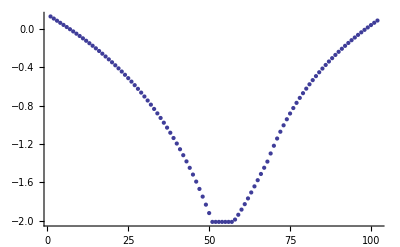

```mathematica
val=Table[ResultL[[i,1]],{i,Length[ResultL]}]
ListPlot[val]
ClearAll[val]
```

```mathematica
Length[ListETotalL]
Length[ResultIJL]
```

102

102

```mathematica
(*DeformElastL2=Table[ToIJ[ListETotalL2[[i]]-FromIJ[ResultIJL2[[i,2]]]],{i,1,Length[ResultL2]}];
SigElastIJL2=Table[{K DeformElastL2[[i,1]],2 G DeformElastL2[[i,2]],DeformElastL2[[i,3]]}/.exemple,{i,1,Length[ResultL2]}];
SigElastIJLplot=Table[{K DeformElastL2[[i,1]],2 G DeformElastL2[[i,2]]}/.exemple,{i,1,Length[ResultL2]}];
gl=ListPlot[SigElastIJLplot]
Show[gl,bg]
Diff=Table[SigElastIJL2[[i]]-ResultIJL2[[i,3]],{i,1,Length[ResultL2]}]//Chop
Table[Function1[ResultIJL2[[i,3,1]],ResultIJL2[[i,3,2]]],{i,1,Length[ResultL2]}]*)
```

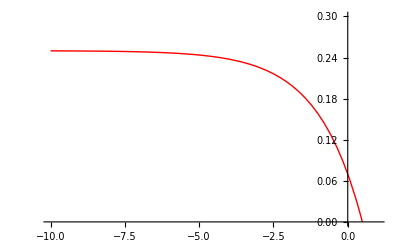

```mathematica
bg
```

```mathematica
ResultIJL[[2,4]]
ToIJ[ListETotalL[[2]]]
FromIJ[ResultIJL[[2,2]]]
ToIJ[ListETotalL[[2]]-FromIJ[ResultIJL[[2,2]]]]
```

{-0.26,0.0600444,1}

{-0.0013,0.000750555,1}

{-0.000838619,-0.000217913}

{-0.0000255553,0.000392191,1}

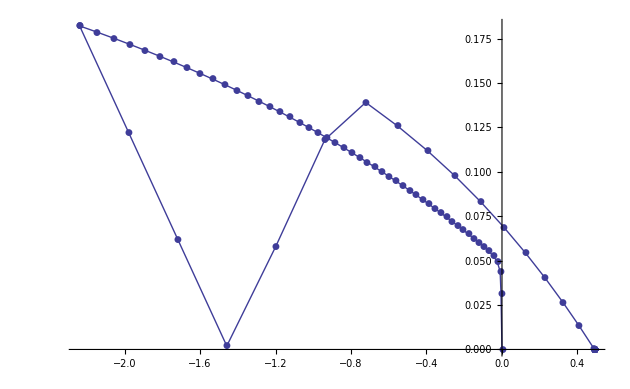

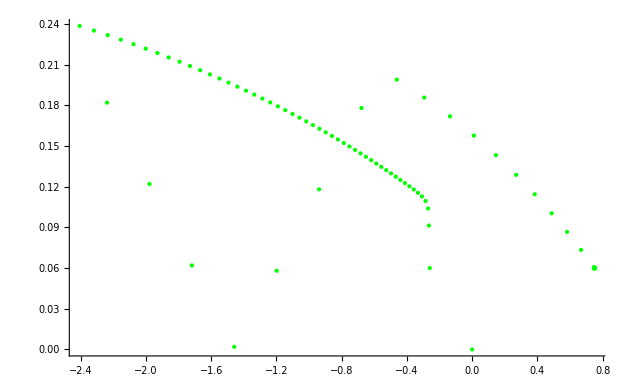

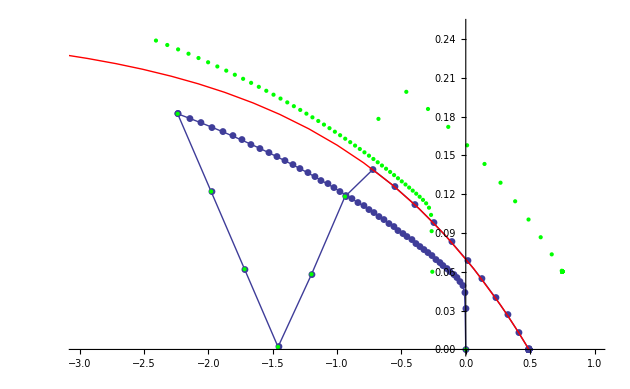

{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,-2},{0,0,-2},{0,0,-2},{0,0,-2},{0,0,-2},{0,0,-2},{0,0,-2},{0,0,-2},{0,0,-2},{0,0,-2},{0,0,-2},{0,0,-2},{0,0,-2},{0,0,-2},{0,0,-2},{0,0,-2},{0,0,-2},{0,0,-2},{0,0,-2},{0,0,-2},{0,0,-2},{0,0,-2},{0,0,-2},{0,0,-2},{0,0,-2},{0,0,-2},{0,0,-2},{0,0,-2},{0,0,-2},{0,0,-2},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}

{-0.07,-0.0392401,-0.0272456,-0.023576,-0.0228031,-0.0229942,-0.023504,-0.0241149,-0.0247519,-0.0253883,-0.0260141,-0.0266254,-0.0272203,-0.0277978,-0.0283571,-0.0288975,-0.0294185,-0.0299193,-0.0303991,-0.0308574,-0.0312934,-0.0317062,-0.032095,-0.0324589,-0.032797,-0.0331084,-0.0333919,-0.0336464,-0.0338708,-0.0340639,-0.0342244,-0.0343508,-0.0344417,-0.0344955,-0.0345107,-0.0344853,-0.0344177,-0.0343057,-0.0341474,-0.0339405,-0.0336827,-0.0333716,-0.0330046,-0.0325791,-0.0320923,-0.0315414,-0.0309235,-0.0302358,-0.0294755,-0.02864,-0.027727,-0.027727,-0.0801263,-0.131071,-0.180284,-0.111275,-0.0358842,2.77556×10^-17,2.77556×10^-17,2.77556×10^-17,2.77556×10^-17,2.77556×10^-17,2.77556×10^-17,2.77556×10^-17,0.,0.,-2.77556×10^-17,0.,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17}

```mathematica
DeformElastL=Table[ToIJ[ListETotalL[[i]]-FromIJ[ResultIJL[[i,2]]]],{i,1,Length[ListETotalL]}];
SigElastIJL=Table[{3K DeformElastL[[i,1]],2 G DeformElastL[[i,2]],DeformElastL[[i,3]]}/.exemple,{i,1,Length[ListETotalL]}];
SigElastIJL2=Table[{3K DeformElastL[[i,1]],2 G DeformElastL[[i,2]]}/.exemple,{i,1,Length[ListETotalL]}];
SigTrialIJL=Table[{ResultIJL[[i,4,1]],ResultIJL[[i,4,2]]},{i,Length[ResultIJL]}];
gl=ListPlot[SigElastIJL2,PlotJoined->True,PlotMarkers->Automatic]
gl2=ListPlot[SigTrialIJL,PlotStyle->{Green}]
Show[gl,bg,gl2,PlotRange->{{-3,1},{0,0.25}}]
Diff=Table[SigElastIJL[[i]]-ResultIJL[[i,3]],{i,1,Length[ListETotalL]}]//Chop
Table[Function1[ResultIJL[[i,3,1]],ResultIJL[[i,3,2]]],{i,1,Length[ListETotalL]}]
```

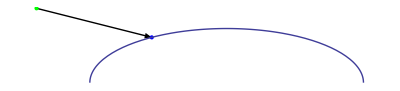

```mathematica
ShowPoint[i_]:=Block[{frompoint,topoint,arrow,dot1,dot2,ellips},
frompoint={ResultIJL[[i,4,1]],ResultIJL[[i,4,2]]};
topoint={ResultIJL[[i,3,1]],ResultIJL[[i,3,2]]};
arrow=Graphics[{Arrowheads[0.02],Arrow[{frompoint,topoint}]}];
dot1=Graphics[{PointSize[Large],Green,Point[frompoint]}];
dot2=Graphics[{PointSize[Large],Blue,Point[topoint]}];
ellips=Ag[ResultL[[i,1]]];
{arrow,dot1,dot2,ellips}
]
Show[ShowPoint[20]]
```

```mathematica
Animate[Show[ShowPoint[i],PlotRange->{{-3,2},{-0.1,0.4}}],{i,1,Length[ResultIJL],1},AnimationRunning->False]
```

```mathematica
Animate[Show[gl,bg,gl2,ShowPoint[i],PlotRange->{{-3,1},{0,0.25}}],{i,1,Length[ResultIJL],1},AnimationRunning->False]
```

```mathematica
TableShowPoint=Table[Show[gl,bg,gl2,ShowPoint[i],PlotRange->{{-3,1},{0,0.25}}],{i,1,Length[ResultIJL]}];
string=NotebookDirectory[];
FileAnimationL=string<>"AnimationL.gif";
Export[FileAnimationL,TableShowPoint]
```

/Users/nathanshauer/Dropbox/Projeto_LabMec_2011_14/Plasticidade/Aprendizado/AnimationL.gif

{{0.,0},{-0.00325,-0.0501373},{-0.0065,-0.076574},{-0.00975,-0.100828},{-0.013,-0.125118},{-0.01625,-0.149925},{-0.0195,-0.175404},{-0.02275,-0.201626},{-0.026,-0.228642},{-0.02925,-0.256496},{-0.0325,-0.285231},{-0.03575,-0.314891},{-0.039,-0.345524},{-0.04225,-0.377178},{-0.0455,-0.409905},{-0.04875,-0.443756},{-0.052,-0.478787},{-0.05525,-0.515052},{-0.0585,-0.552608},{-0.06175,-0.591511},{-0.065,-0.631817},{-0.065,-0.631817},{-0.06175,-0.386262},{-0.0585,-0.15394},{-0.05525,-0.11208},{-0.052,-0.0731518},{-0.04875,-0.0372249},{-0.0455,-0.00432938},{-0.04225,0.0255477},{-0.039,0.0524629},{-0.03575,0.0765144},{-0.0325,0.0978376},{-0.02925,0.116598},{-0.026,0.132986},{-0.02275,0.147203},{-0.0195,0.159461},{-0.01625,0.163435},{-0.013,0.163435},{-0.00975,0.163435},{-0.0065,0.163435},{-0.00325,0.163435},{0.,0.163435}}

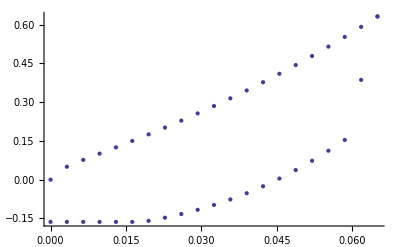

```mathematica
a=Table[{ListETotalL[[i,1]],ResultL[[i,3,1]]},{i,1,Length[ListETotalL]}]
ga=ListPlot[-a]
Clear[a,b,ga,gb]
```

```mathematica
a=Derivatives[Result[[1,3]],Result[[2,3]]-Result[[1,3]],Result[[1,1]]];
{{a[[1,1]]Sqrt[3],a[[1,2]]},{a[[2,1]]Sqrt[3],a[[2,2]]},a[[3]]}
{ListETotal[[2]],Result[[2,2]],Result[[2,1]]}
```

lval = 0.133045

flval = 0.0532179

gradf2 = {-26.0371,0.}

derivT = {-0.00191967,0.0157458}

dlval = 17.0081

B lval = 0.08914

- C B E^(B lval) = -0.131844

dfval = -2.24242

one = 255.675

two = 84.2732

three = 0.

four = 0.

df2depsp = 339.949

epspponto = -0.00014703

trN2 = -45.0976

gammaponto = 3.26026×10^-6

deformPlast = {-0.0000848878,0.}

ST = {0,1}

deformElast = {-0.0000166248,0.000196822}

{{-0.000175825,0.000196822},{-0.00014703,0.},-0.00014703}

{{-0.000325,0.000187639},{-0.000275126,0.0000484644},-0.000275126}

```mathematica
ElastoPlastic[Result[[1,1]],Result[[1,2]],ListETotal[[2]]]
```

ETotal = {-0.000325,0.000187639}

SigI1xJ2 = {-0.0216667,0.0150111}

valf2 = 0.431788

subit {I1T→-0.0216667,J2T→0.0150111}

θ = -π

θ = -(19 π)/20

θ = -(9 π)/10

θ = -(17 π)/20

θ = -(4 π)/5

θ = -(3 π)/4

θ = -(7 π)/10

θ = -(13 π)/20

θ = -(3 π)/5

θ = -(11 π)/20

θ = -π/2

θ = -(9 π)/20

θ = -(2 π)/5

θ = -(7 π)/20

θ = -(3 π)/10

θ = -π/4

θ = -π/5

θ = -(3 π)/20

θ = -π/10

θ = -π/20

θ = 0

θ = π/20

θ = π/10

θ = (3 π)/20

θ = π/5

θ = π/4

θ = (3 π)/10

θ = (7 π)/20

θ = (2 π)/5

θ = (9 π)/20

θ = π/2

θ = (11 π)/20

θ = (3 π)/5

θ = (13 π)/20

θ = (7 π)/10

θ = (3 π)/4

θ = (4 π)/5

θ = (17 π)/20

θ = (9 π)/10

θ = (19 π)/20

θ = π

restheta = {5.67729,5.34003,5.12872,4.9867,4.87787,4.78283,4.69152,4.5989,4.5027,4.4021,4.29704,4.18782,4.07487,3.9587,3.83975,3.71847,3.59526,3.47045,3.34437,3.21729,3.08947,2.96115,3.45065,3.57936,3.70797,3.83632,3.96425,4.09163,4.21839,4.34455,4.47028,4.59604,4.72284,4.85265,4.98938,5.14073,5.32211,5.56417,5.91817,0.122311,0.605891}

θ = (19 π)/20

θ = (19 π)/20

residue = {0.122311,0.00034957}

tangent = {{3.32067,-242.53},{-0.000312192,1.33818}}

delu = {0.0568818,0.000274499}

θ = 2.92763

delepsp = -0.000274499

θ = 2.92763

residue = {-0.0229419,3.22682×10^-6}

tangent = {{4.02657,-202.504},{-0.000428652,1.33871}}

delu = {-0.00566767,5.95617×10^-7}

θ = 2.9333

delepsp = -0.000275094

θ = 2.9333

residue = {0.0000914666,3.16371×10^-8}

tangent = {{4.05591,-225.014},{-0.000417475,1.33881}}

delu = {0.0000242825,3.12026×10^-8}

θ = 2.93327

delepsp = -0.000275126

θ = 2.93327

residue = {-1.41228×10^-9,5.93007×10^-13}

tangent = {{4.05592,-224.935},{-0.000417523,1.33881}}

delu = {-3.29334×10^-10,3.40229×10^-13}

θ = 2.93327

delepsp = -0.000275126

θ = 2.93327

residue = {0.,1.6263×10^-19}

tangent = {{4.05592,-224.935},{-0.000417523,1.33881}}

delu = {6.85528×10^-18,1.23612×10^-19}

θ = 2.93327

delepsp = -0.000275126

θ = 2.93327

residue = {0.,5.42101×10^-20}

Function2 = 2.22045×10^-16

{-0.000275126,{-0.000275126,0.0000484644},{-0.00332496,0.011134}}

```mathematica
{K,2G}/.exemple
{ListETotal[[2,1]]K,ListETotal[[2,2]]2G}/.exemple
(%-Result[[2,3]])/.exemple
{%[[1]]/K,%[[2]]/(2G)}/.exemple
```

{66.6667,80}

{-0.216667,0.150111}

{-0.179007,0.117562}

{-0.0026851,0.00146953}

```mathematica
Result[[2]]
```

{-0.000275126,{-0.000275126,0.0000484644},{-0.00332496,0.011134}}

```mathematica
epsp=Result[[2,1]]
theta=2.5604883056356527;
l=LFunction[epsp];
fl=F[l]/.exemple;
i1theta=l+fl R Cos[theta]/.exemple;
i1=Result[[2,3,1]];
i1-i1theta;
sqj2=Result[[2,3,2]];
sqj2theta=fl Sin[theta];
sqj2theta-sqj2;
(l-i1)^2 /(fl R)^2 + sqj2^2/fl^2 -1/.exemple;
gfv1=2√3(i1-l)/(fl R)^2/.exemple;
√3 gfv1;
gfv2=√2 sqj2/fl^2;
sqj2/fl;
ep=Result[[2,2]];
ArcTan[ep[[1]],ep[[2]]]
epprop={6(i1-l)/(fl R)^2,(2sqj2)/fl^2}/.exemple
ArcTan[epprop[[1]],epprop[[2]]]
TmTt={K epprop[[1]],2G epprop[[2]]}/.exemple
sigtrial={ListETotal[[2,1]]K,ListETotal[[2,2]]2G}/.exemple;
sigma=Result[[2,3]]
difsigma=(sigtrial-sigma)/.exemple;
ArcTan[difsigma[[1]],difsigma[[2]]]
ep-{difsigma[[1]]/K,difsigma[[2]]/(2G)}/.exemple
ArcTan[TmTt[[1]],TmTt[[2]]]
ArcTan[2 G R difsigma[[1]],3K difsigma[[2]]]/.exemple
theta
difsigma

Print[" delta gamma ",δγ2=epsp/epprop[[1]]]
Tepprop={K epprop[[1]],2G epprop[[2]]}/.exemple;
toto=Tepprop δγ2
ArcTan[difsigma[[1]],difsigma[[2]]]
ArcTan[toto[[1]],toto[[2]]]
δγ2 epprop-ep


Print["Checking stress functions"];
sigma
sqj2
l
fl
Print["gradf ",{epprop[[1]]/Sqrt[3],epprop[[2]]/Sqrt[2]}]
{sigma[[1]]/Sqrt[3],sigma[[2]]Sqrt[2]}

DLFunction[epsp]
B l/.exemple
dF[l]/.exemple
DLFunction[epsp]dF[l]/.exemple
a=DLFunction[epsp](2(l-i1))/(fl R)^2/.exemple
b=DLFunction[epsp](-(2(l-i1)^2)/(fl^3 R^2)dF[l])/.exemple
c=DLFunction[epsp](-(2sigma[[2]]^2)/fl^3 dF[l])/.exemple
Print["four ",DLFunction[epsp](-(2sigma[[2]]^2)/1 dF[l])/.exemple]
dfedep=DLFunction[epsp]((2(l-i1))/(fl R)^2-(2(l-i1)^2)/(fl^3 R^2)dF[l]-(2sqj2^2)/fl^3 dF[l])/.exemple
gradFT=epprop[[1]] sigma[[1]]/3+epprop[[2]] sigma[[2]]
(*Function2[sigma[[1]],sigma[[2]],epsp]-Function2[0,0,epsp]
Function2[sigma[[1]],sigma[[2]],0]-Function2[0,0,0]
*)
Print["epponto " ,a=epponto=-gradFT/dfedep]
Print["TrN2 ",epprop[[1]]]
Print["gammaponto ",gammaponto=epponto/epprop[[1]]]

epsp=0;
i1=0;
sqj2=0;
epprop={6(i1-l)/(fl R)^2,(2sqj2)/fl^2}/.exemple;
dfedep=DLFunction[epsp]((2(l-i1))/(fl R)^2-(2(l-i1)^2)/(fl^3 R^2)dF[l]-(2sqj2^2)/fl^3 dF[l])/.exemple
gradFT=epprop[[1]] sigma[[1]]/3+epprop[[2]] sigma[[2]]
(*Function2[sigma[[1]],sigma[[2]],epsp]-Function2[0,0,epsp]
Function2[sigma[[1]],sigma[[2]],0]-Function2[0,0,0]
*)
Print["epponto " ,b=epponto=-gradFT/dfedep]
Print["epponto medio ",(a+b)/2]
Print["TrN2 ",epprop[[1]]]
Print["gammaponto ",gammaponto=epponto/epprop[[1]]]


ClearAll[l,fl,i1,sqj2,gfv1,gfv2,epsp,theta,i1theta,sqj2theta,ep,epprop,TmTt,sigtrial,sigma,difsigma,Tepprop,toto,δγ2,dfedep,gradFT,epponto,a,b,c,gammaponto]
```

-0.000275126

2.96723

{-43.6165,7.68321}

2.96723

{-2907.77,614.657}

{-0.00332496,0.011134}

2.93327

{0.,0.}

2.93327

2.93327

2.56049

{-0.0183417,0.00387715}

delta gamma 6.30783×10^-6

{-0.0183417,0.00387715}

2.93327

2.93327

{5.42101×10^-20,-4.06576×10^-20}

Checking stress functions

{-0.00332496,0.011134}

0.011134

0.128354

0.0538354

gradf {-25.182,5.43285}

{-0.00191967,0.0157458}

17.0926

0.0859971

-0.13143

-2.24649

248.507

79.888

3.56967

four 0.000556972

331.965

0.133886

epponto -0.000403313

TrN2 -43.6165

gammaponto 9.2468×10^-6

316.564

0.0471204

epponto -0.00014885

epponto medio -0.000276081

TrN2 -42.5151

gammaponto 3.5011×10^-6

```mathematica
K
```

K